# Adaptive meiotic drive in selfing populations with heterozygote advantage

```mathematica
Clear[Wmean, ABABprime, ABAbprime, AbAbprime, ABaBprime, Ababprime, ABabprime, AbaBprime, aBaBprime, aBabprime, ababprime, ABAB, ABAb, AbAb, ABaB, Abab, ABab, AbaB, aBaB, aBab, abab, eggAB, eggAb, eggaB, eggab, spermAB, spermAb, spermaB, spermab, JacobianSelfing, JacobianSelfing2, JmutSelf, JmutAllandNone, ks1, ke1, ks2, ke2, r,wAA, wAa, waa, S, x, y, z, xa,ya, za, xprime, yprime, zprime, F, Fprime, p, prime, q,qprime, u, v, w, wa, qhat, Fhat, xhat, yhat, zhat, qa, pa, JmutEigens, JmutEigens2, FSmat, FSmatT,RightEigenVs,LeftEigenVs,RightNormV, LeftNormV, u0,SummationTotal];
```

## Model

```mathematica
Wmean = ABAB*(wAA) + ABAb*(wAA) + AbAb*(wAA)+ABaB*(wAa) + Abab*(wAa) + ABab*(wAa) + AbaB*(wAa)+aBaB*(waa)+aBab*(waa)+abab*(waa);
```

The following model assumes a two-locus diploid population segregating for two-alleles at each of loci A (“A” and “a”) and B (“B” and “b”). The segregation parameters ke1, ke2, km1, km2 correspond to k_f0, k_f, k_m0, k_m, respectively; the latter set appear in the text of the article. A generalized formulation of the two-locus haplotype frequencies in sperm and eggs is given by:

```mathematica
eggAB = (1/Wmean)*(ABAB*(wAA)*(1) + ABAb*(wAA)*(1/2) + AbAb*(wAA)*(0) + ABaB*(wAa)*(1-ke1) + Abab*(wAa)*(0) +ABab*(wAa)*(1-r)*(1-ke2)+AbaB*(wAa)*(r)*(1-ke2)+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
eggAb = (1/Wmean)*(ABAB*(wAA)*(0) + ABAb*(wAA)*(1/2) + AbAb*(wAA)*(1) + ABaB*(wAa)*(0) + Abab*(wAa)*(1-ke2) +ABab*(wAa)*(r)*(1-ke2)+AbaB*(wAa)*(1-r)*(1-ke2)+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
eggaB = (1/Wmean)*(ABAB*(wAA)*(0) + ABAb*(wAA)*(0) + AbAb*(wAA)*(0) + ABaB*(wAa)*(ke1) + Abab*(wAa)*(0) +ABab*(wAa)*(r)*(ke2)+AbaB*(wAa)*(1-r)*(ke2)+aBaB*(waa)*(1) + aBab*(waa)*(1/2) +abab*(waa)*(0));
```

```mathematica
eggab = (1/Wmean)*(ABAB*(wAA)*(0) + ABAb*(wAA)*(0) + AbAb*(wAA)*(0) + ABaB*(wAa)*(0) + Abab*(wAa)*(ke2) +ABab*(wAa)*(1-r)*(ke2)+AbaB*(wAa)*(r)*(ke2)+aBaB*(waa)*(0) + aBab*(waa)*(1/2) +abab*(waa)*(1));
```

```mathematica
spermAB = (1/Wmean)*(ABAB*(wAA)*(1) + ABAb*(wAA)*(1/2) + AbAb*(wAA)*(0) + ABaB*(wAa)*(1-ks1) + Abab*(wAa)*(0) +ABab*(wAa)*(1-r)*(1-ks2)+AbaB*(wAa)*(r)*(1-ks2)+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
spermAb = (1/Wmean)*(ABAB*(wAA)*(0) + ABAb*(wAA)*(1/2) + AbAb*(wAA)*(1) + ABaB*(wAa)*(0) + Abab*(wAa)*(1-ks2) +ABab*(wAa)*(r)*(1-ks2)+AbaB*(wAa)*(1-r)*(1-ks2)+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
spermaB = (1/Wmean)*(ABAB*(wAA)*(0) + ABAb*(wAA)*(0) + AbAb*(wAA)*(0) + ABaB*(wAa)*(ks1) + Abab*(wAa)*(0) +ABab*(wAa)*(r)*(ks2)+AbaB*(wAa)*(1-r)*(ks2)+aBaB*(waa)*(1) + aBab*(waa)*(1/2) +abab*(waa)*(0));
```

```mathematica
spermab = (1/Wmean)*(ABAB*(wAA)*(0) + ABAb*(wAA)*(0) + AbAb*(wAA)*(0) + ABaB*(wAa)*(0) + Abab*(wAa)*(ks2) +ABab*(wAa)*(1-r)*(ks2)+AbaB*(wAa)*(r)*(ks2)+aBaB*(waa)*(0) + aBab*(waa)*(1/2) +abab*(waa)*(1));
```

These gametes unite at random to form a proportion (1-S) of the offspring generation. The remainder of the offspring generation (S) is formed by self-fertilization. Importantly, male and female segregation ratios are subject to evolution, as the “b” allele changes the segregation scheme so that “a” is favored with probability “ks2” in male meiosis and “ke2” in female meiosis, in contrast to their original values of “ks1” and “ke1”, respectively.

The generalized dynamical system for the 10 diploid two-locus genotype proportions is given by:

```mathematica
ABABprime = (1-S)*(spermAB*eggAB) + (1/Wmean)*S*(ABAB*(wAA)*(1) + ABAb*(wAA)*(1/4)+ AbAb*(wAA)*(0)+ABaB*(wAa)*((1-ks1)*(1-ke1)) + Abab*(wAa)*(0)+ABab*(wAa)*((1-r)^2)*((1-ks2)*(1-ke2)) + AbaB*(wAa)*(r^2)*((1-ks2)*(1-ke2))+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
ABAbprime = (1-S)*((spermAB*eggAb) +(spermAb*eggAB))+ (1/Wmean)*S*(ABAB*(wAA)*(0) +ABAb*(wAA)*(1/2)+ AbAb*(wAA)*(0)+ABaB*(wAa)*(0) + Abab*(wAa)*(0)+ABab*(wAa)*(2*r*(1-r)*((1-ks2)*(1-ke2))) + AbaB*(wAa)*(2*r*(1-r)*((1-ks2)*(1-ke2)))+aBaB*(waa)*(0) +aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
AbAbprime=(1-S)*(spermAb*eggAb)+(1/Wmean)*S*(ABAB*(wAA)*(0) + ABAb*(wAA)*(1/4)+ AbAb*(wAA)*(1)+ABaB*(wAa)*(0) + Abab*(wAa)*((1-ks2)*(1-ke2))+ABab*(wAa)*((r^2)*((1-ks2)*(1-ke2))) + AbaB*(wAa)*(((1-r)^2)*((1-ks2)*(1-ke2)))+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
ABaBprime=(1-S)*((spermAB*eggaB)+(spermaB*eggAB))+(1/Wmean)*S*(ABAB*(wAA)*(0) +ABAb*(wAA)*(0)+ AbAb*(wAA)*(0)+ABaB*(wAa)*(ks1*(1-ke1)+(1-ks1)*ke1) + Abab*(wAa)*(0)+ABab*(wAa)*(r*(1-r)*(ks2*(1-ke2)+(1-ks2)*ke2)) + AbaB*(wAa)*(r*(1-r)*(ks2*(1-ke2)+(1-ks2)*ke2))+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
Ababprime = (1-S)*((spermAb*eggab)+(spermab*eggAb))+(1/Wmean)*S*(ABAB*(wAA)*(0) +ABAb*(wAA)*(0)+AbAb*(wAA)*(0)+ABaB*(wAa)*(0) + Abab*(wAa)*(ks2*(1-ke2)+(1-ks2)*ke2)+ABab*(wAa)*(r*(1-r)*(ks2*(1-ke2)+(1-ks2)*ke2)) + AbaB*(wAa)*(r*(1-r)*(ks2*(1-ke2)+(1-ks2)*ke2))+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
ABabprime=(1-S)*((spermAB*eggab)+(spermab*eggAB))+ (1/Wmean)*S*(ABAB*(wAA)*(0) +ABAb*(wAA)*(0)+ AbAb*(wAA)*(0)+ABaB*(wAa)*(0) + Abab*(wAa)*(0)+ABab*(wAa)*(((1-r)^2)*(ks2*(1-ke2)+(1-ks2)*ke2)) + AbaB*(wAa)*((r^2)*(ks2*(1-ke2)+(1-ks2)*ke2))+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
AbaBprime = (1-S)*((spermAb*eggaB)+(spermaB*eggAb))+(1/Wmean)*S*(ABAB*(wAA)*(0) +ABAb*(wAA)*(0)+AbAb*(wAA)*(0)+ABaB*(wAa)*(0) + Abab*(wAa)*(0)+ABab*(wAa)*((r^2)*(ks2*(1-ke2)+(1-ks2)*ke2)) + AbaB*(wAa)*(((1-r)^2)*(ks2*(1-ke2)+(1-ks2)*ke2))+aBaB*(waa)*(0) + aBab*(waa)*(0) +abab*(waa)*(0));
```

```mathematica
aBaBprime = (1-S)*(spermaB*eggaB)+(1/Wmean)*S*(ABAB*(wAA)*(0) +ABAb*(wAA)*(0)+ AbAb*(wAA)*(0)+ABaB*(wAa)*(ks1*ke1) + Abab*(wAa)*(0)+ABab*(wAa)*((r^2)*(ks2*ke2)) + AbaB*(wAa)*(((1-r)^2)*(ks2*ke2))+aBaB*(waa)*(1) + aBab*(waa)*(1/4) +abab*(waa)*(0));
```

```mathematica
aBabprime=(1-S)*((spermaB*eggab)+(spermab*eggaB))+(1/Wmean)*S*(ABAB*(wAA)*(0) + ABAb*(wAA)*(0)+AbAb*(wAA)*(0)+ABaB*(wAa)*(0) +Abab*(wAa)*(0)+ABab*(wAa)*(2*r*(1-r)*(ks2*ke2)) + AbaB*(wAa)*(2*r*(1-r)*(ks2*ke2))+aBaB*(waa)*(0) + aBab*(waa)*(1/2) +abab*(waa)*(0));
```

```mathematica
ababprime=(1-S)*(spermab*eggab)+(1/Wmean)*S*(ABAB*(wAA)*(0) + ABAb*(wAA)*(0)+ AbAb*(wAA)*(0)+ABaB*(wAa)*(0) + Abab*(wAa)*(ks2*ke2)+ABab*(wAa)*(((1-r)^2)*(ks2*ke2)) + AbaB*(wAa)*((r^2)*(ks2*ke2))+aBaB*(waa)*(0) + aBab*(waa)*(1/4) +abab*(waa)*(1));
```

Since the goal is to determine the long-term stability of a partially (or fully) selfing population to mutants that induce adaptive meiotic drive, a Jacobian matrix will be evaluated at an equilibrium so as to yield an upper-triangular block matrix. The upper-left 3x3 matrix will correspond to a population never subject to mutant modifiers of drive. The lower-right 7x7 matrix will correspond to the presence of infinitesimal amounts of the mutant drive-modifier. The specifications listed after the matrix will include that r = 1/2 (the case of an unlinked modifier of drive), that heterozygote fitness is set to 1, and that the homozygote fitnesses are equal to wG. But first, I examine is a single-locus Mendelian equilibrium in a selfing population with symmetric overdominance.

## The single-locus Mendelian equilibrium

### One-locus model

Before working with the Jacobian, the conditions for a single-locus equilibrium must be investigated. The formulation follows closely that of Burt and Trivers (1999), but here assumes fair meiosis and heterozygote advantage.

```mathematica
Clear[x,y,z,xa,ya,za,F,p,q,w,wG,w2,wAA,waa,ks1,ke1,pa,qa, Fprime,S]
```

```mathematica
p = 1-q;
```

```mathematica
x =  (p^2)+F*p*q;
```

```mathematica
y = 2*p*q*(1-F);
```

```mathematica
z = q^2+F*p*q;
```

```mathematica
w = x*(wAA) +y +z*(waa);
```

```mathematica
xa = x*(wAA/w);
```

```mathematica
ya = y*(1/w);
```

```mathematica
za = z*(waa/w);
```

```mathematica
pa = ya*(1/2)+xa;
```

```mathematica
qa= ya*(1/2) +za;
```

```mathematica
xprime = S*(xa+ya*(1/4))+(1-S)*(pa^2);
```

```mathematica
yprime = S*ya*(1/2)+(1-S)*(2*pa*qa);
```

```mathematica
zprime = S*(za +ya*(1/4))+(1-S)*(qa^2);
```

```mathematica
pprime = xprime +yprime/2;
```

```mathematica
qprime = Simplify[zprime + yprime/2 /. {wAA -> wG, waa -> wG}];
```

```mathematica
Fprime = Simplify[1 - yprime/(2*pprime*qprime)/. {wAA -> wG, waa -> wG}]
```

(S (-1+F (1+4 q (-1+wG)-4 q^2 (-1+wG)-2 wG)-2 q (-1+wG)+2 F^2 (-1+q) q (-1+wG)+2 q^2 (-1+wG)) wG)/(2 ((-1+F) q (-1+wG)+wG) (-1+q+F (-1+q) (-1+wG)-q wG))

```mathematica
wa = Simplify[(qprime/pprime)/(q/p)/.{wAA -> wG, waa -> wG}]
```

(1+q (-1+wG)+F (-1+q+wG-q wG))/((-1+F) q (-1+wG)+wG)

### Equilibria

Upon obtaining expressions for the fitness of the “a” allele (wa) and the inbreeding coefficient (F), the equilibria can be obtained.

```mathematica
Simplify[Solve[wa ==1 &&  Fprime-F==0, {q,F}]]
```

{{q→1/2,F→-(1+wG-S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(2 (-1+wG))},{q→1/2,F→(-1+(-1+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(2 (-1+wG))}}

Here I test for the biological feasibility of the equilibria. That is, I test whether the inbreeding coefficient generally lies in [-1,1].

```mathematica
Reduce[-1≤ -(1+wG-S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(2 (-1+wG))≤1&&0≤wG<1&&0<S≤ 1,{S,wG}]
```

(0<S<1&&wG==0)||(S==1&&0≤wG≤1/2)

```mathematica
Reduce[-1≤ (-1+(-1+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(2 (-1+wG))≤1&&0≤wG<1&& 0<S≤ 1,{S,wG}]
```

0<S≤1&&0≤wG<1

### Feasibility

Assuming balanced lethality, the first equilibrium in “F” is biologically nonsensical, since homozygote lethality and a maximal excess of homozygotes (F = 1) cannot simultaneously occur:

```mathematica
-(1+wG-S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(2 (-1+wG))/.{wG-> 0}
```

1

```mathematica
(-1+(-1+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(2 (-1+wG))/.{wG->0}
```

0

Assuming full selfing and homozygote fitness in the interval (0, 1/2], the first equilibrium in “F” corresponds to a population composed of AA and aa genotypes only, regardless of the parameter value (in fact, regardless of allele frequency, as can be seen by using the Solve function above with S set to 1). This equilibrium is of no interest to the problem at hand, since such a population cannot express heterozygote advantage. The second equilibrium is clearly the relevant one for a population with a non-zero proportion of heterozygotes:

```mathematica
-(1+wG-S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(2 (-1+wG)) /. {S->1, wG->0.45}
```

1.

```mathematica
(-1+(-1+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(2 (-1+wG)) /. {S->1, wG->0.45}
```

0.818182

### Internal stability

The preceding analysis identifies the biologically relevant equilibrium of q and F:

```mathematica
qhat =1/2;
```

```mathematica
Fhat =(-1+(-1+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(2 (-1+wG));
```

```mathematica
Fhat //TraditionalForm
```

(√((S+1)^2 wG^2+(2-6 S) wG+1)+(S-1) wG-1)/(2 (wG-1))

Given qhat and Fhat, the equilibrium in terms of genotypic proportions is:

```mathematica
xhat = Simplify[(1-qhat)^2+(1-qhat)*(qhat)*Fhat ]
```

(-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))

```mathematica
yhat = Simplify[2*(1-qhat)*(qhat)*(1-Fhat)]
```

-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))

```mathematica
zhat = Simplify[(qhat)^2+(1-qhat)*(qhat)*Fhat]
```

(-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))

Here I set up the Jacobian, derive eigenvalues, and test for stability.

```mathematica
Simplify[{{D[qprime,q],D[qprime,F]},{D[Fprime,q], D[Fprime,F]}}/. {q-> qhat, F -> Fhat}]
```

{{(4 wG)/(1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)),0},{0,(8 S wG)/((1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))^2)}}

```mathematica
Eigenvalues[{{(4 wG)/(1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)),0},{0,(8 S wG)/((1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))^2)}}]
```

{(8 S wG)/((1+wG+S wG+√(1+2 wG-6 S wG+wG^2+2 S wG^2+S^2 wG^2))^2),(4 wG (1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/((1+wG+S wG+√(1+2 wG-6 S wG+wG^2+2 S wG^2+S^2 wG^2))^2)}

```mathematica
Reduce[(8 S wG)/((1+wG+S wG+√(1+2 wG-6 S wG+wG^2+2 S wG^2+S^2 wG^2))^2)<1 && (4 wG (1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/((1+wG+S wG+√(1+2 wG-6 S wG+wG^2+2 S wG^2+S^2 wG^2))^2)<1&&(0<S≤1&&0≤wG<1)]
```

(0≤wG<1/2&&0<S≤1)||(1/2≤wG<1&&0<S<1)

The above concludes the analysis of internal stability for the single-locus equilibrium.

## Evolutionary invasion analysis of drive-enhancers in a Mendelian population

### Jacobian

```mathematica
JacobianSelfing=
{{D[ABABprime, ABAB],D[ABABprime, aBaB], D[ABABprime, ABaB],D[ABABprime, ABAb],D[ABABprime, ABab], D[ABABprime, AbaB],D[ABABprime, aBab],D[ABABprime, AbAb],D[ABABprime, Abab],  D[ABABprime, abab]},{D[aBaBprime, ABAB],D[aBaBprime, aBaB], D[aBaBprime, ABaB],D[aBaBprime, ABAb],D[aBaBprime, ABab], D[aBaBprime, AbaB],D[aBaBprime, aBab],D[aBaBprime, AbAb],D[aBaBprime, Abab],  D[aBaBprime, abab]},
{D[ABaBprime, ABAB],D[ABaBprime, aBaB], D[ABaBprime, ABaB],D[ABaBprime, ABAb],D[ABaBprime, ABab], D[ABaBprime, AbaB],D[ABaBprime, aBab],D[ABaBprime, AbAb],D[ABaBprime, Abab],  D[ABaBprime, abab]},
{D[ABAbprime, ABAB],D[ABAbprime, aBaB], D[ABAbprime, ABaB],D[ABAbprime, ABAb],D[ABAbprime, ABab], D[ABAbprime, AbaB],D[ABAbprime, aBab],D[ABAbprime, AbAb],D[ABAbprime, Abab],  D[ABAbprime, abab]},
{D[ABabprime, ABAB],D[ABabprime, aBaB], D[ABabprime, ABaB],D[ABabprime, ABAb],D[ABabprime, ABab], D[ABabprime, AbaB],D[ABabprime, aBab],D[ABabprime, AbAb],D[ABabprime, Abab],  D[ABabprime, abab]},
{D[AbaBprime, ABAB],D[AbaBprime, aBaB], D[AbaBprime, ABaB],D[AbaBprime, ABAb],D[AbaBprime, ABab], D[AbaBprime, AbaB],D[AbaBprime, aBab],D[AbaBprime, AbAb],D[AbaBprime, Abab],  D[AbaBprime, abab]},
{D[aBabprime, ABAB],D[aBabprime, aBaB], D[aBabprime, ABaB],D[aBabprime, ABAb],D[aBabprime, ABab], D[aBabprime, AbaB],D[aBabprime, aBab],D[aBabprime, AbAb],D[aBabprime, Abab],  D[aBabprime, abab]},
{D[AbAbprime, ABAB],D[AbAbprime, aBaB], D[AbAbprime, ABaB],D[AbAbprime, ABAb],D[AbAbprime, ABab], D[AbAbprime, AbaB],D[AbAbprime, aBab],D[AbAbprime, AbAb],D[AbAbprime, Abab],  D[AbAbprime, abab]},
{D[Ababprime, ABAB],D[Ababprime, aBaB], D[Ababprime, ABaB],D[Ababprime, ABAb],D[Ababprime, ABab], D[Ababprime, AbaB],D[Ababprime, aBab],D[Ababprime, AbAb],D[Ababprime, Abab],  D[Ababprime, abab]},
{D[ababprime, ABAB],D[ababprime, aBaB], D[ababprime, ABaB],D[ababprime, ABAb],D[ababprime, ABab], D[ababprime, AbaB],D[ababprime, aBab],D[ababprime, AbAb],D[ababprime, Abab],  D[ababprime, abab]}}/.{ r->1/2,ke1->1/2,ks1->1/2,  wAA->wG, waa->wG,wAa->1, ABAB->xhat,aBaB->zhat,ABaB->yhat,ABAb->0,ABab->0,AbaB->0,aBab->0,AbAb->0,Abab->0,abab->0}//MatrixForm
```

(-(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(S wG)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+((1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+S/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(S wG)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | -(2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+((1-ke2) (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ke2) (1-ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | -(2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+((1-ke2) (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ke2) (1-ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)
-(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(S wG)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))) | -(2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+((1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+S/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(ke2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ke2 ks2 S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | -(2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(ke2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ke2 ks2 S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(S wG)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(2 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)-(S wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(16 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)
(S wG (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(1-S) (-(4 wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(2 wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | (S wG (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(1-S) (-(4 wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(2 wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | (S (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+S/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (-(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | (S wG (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(1-S) (-(4 wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | (S (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (-(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | (S (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (-(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | (S wG (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(1-S) (-(4 wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | -(4 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(S wG (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(4 (1-S) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(S (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | -(4 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG)))^2)/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^3)+(S wG (1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)
0 | 0 | 0 | ((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(S wG)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | ((1-ke2) (1-ks2) S)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | ((1-ke2) (1-ks2) S)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | 0 | (2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | (1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | 0
0 | 0 | 0 | 0 | ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | ((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | 0 | (1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | (2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)
0 | 0 | 0 | ((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | 0 | (2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2) | (1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | 0
0 | 0 | 0 | 0 | (ke2 ks2 S)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | (ke2 ks2 S)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | ((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(S wG)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | 0 | (1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)) | (2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)
0 | 0 | 0 | (S wG)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | ((1-ke2) (1-ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | ((1-ke2) (1-ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | 0 | (S wG)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))) | ((1-ke2) (1-ks2) S)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))) | 0
0 | 0 | 0 | 0 | ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | 0 | 0 | ((ke2 (1-ks2)+(1-ke2) ks2) S)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))) | 0
0 | 0 | 0 | 0 | (ke2 ks2 S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | (ke2 ks2 S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | (S wG)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))) | 0 | (ke2 ks2 S)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))) | (S wG)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))

```mathematica
JmutSelf={{((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(S wG)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), ((1-ke2) (1-ks2) S)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), ((1-ke2) (1-ks2) S)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), 0, (2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2), (1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), 0}, {0, ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), ((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2), 0, (1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), (2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)}, {((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2), ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), 0, (2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2), (1-S) (((1-ke2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+((1-ks2) (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), 0}, {0, (ke2 ks2 S)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), (ke2 ks2 S)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))))+(1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), ((1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(S wG)/(2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), 0, (1-S) ((ke2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)+(ks2 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)), (2 (1-S) wG (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(8 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(8 (-1+wG))))/((-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))^2)}, {(S wG)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), ((1-ke2) (1-ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), ((1-ke2) (1-ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), 0, (S wG)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))), ((1-ke2) (1-ks2) S)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))), 0}, {0, ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), ((ke2 (1-ks2)+(1-ke2) ks2) S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), 0, 0, ((ke2 (1-ks2)+(1-ke2) ks2) S)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))), 0}, {0, (ke2 ks2 S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), (ke2 ks2 S)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), (S wG)/(4 (-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))), 0, (ke2 ks2 S)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG))), (S wG)/(-(1+(-3+S) wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))/(4 (-1+wG))+(wG (-3+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)))/(4 (-1+wG)))}};
```

### Eigenvalues

```mathematica
JmutEigens=Simplify[Eigenvalues[JmutSelf]]
```

{0,(2 (ke2+ks2-2 ke2 ks2) S)/(1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)),(2 S wG)/(1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)),(2 S wG)/(1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)),(2 (1+S) wG)/(1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)),(1-S+2 ke2 S+2 ks2 S-4 ke2 ks2 S+wG+S wG-1/2 √(64 (-ks2+ke2 (-1+2 ks2)) S wG+4 (1+wG+S (-1+ke2 (2-4 ks2)+2 ks2+wG))^2))/(1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2)),(1-S+2 ke2 S+2 ks2 S-4 ke2 ks2 S+wG+S wG+1/2 √(64 (-ks2+ke2 (-1+2 ks2)) S wG+4 (1+wG+S (-1+ke2 (2-4 ks2)+2 ks2+wG))^2))/(1+wG+S wG+√(1+(2-6 S) wG+(1+S)^2 wG^2))}

```mathematica
Reduce[JmutEigens[[2]]>1 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG≤1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[3]]>1 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG≤1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[4]]>1 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG≤1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[5]]>1 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG≤1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[6]]>1 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG≤1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[7]]>1 && 0≤ks2≤1 &&0≤ke2≤1&&0≤wG<1 && 0<S< 1,{ke2, ks2,wG,S}]
```

(0≤ke2<1/2&&1/2<ks2≤1&&0≤wG<1&&0<S<1)||(1/2<ke2≤1&&0≤ks2<1/2&&0≤wG<1&&0<S<1)

Note that these eigenvalues are uniformly non-negative and real. (Using “Abs” in the “Reduce” functions above seems to take an inordinate amount of time). Here, I check that the terms under radicals are never less than zero, and that the eigenvalues themselves are non-negative. The (geometric) invasion criterion then reduces to checking whether the eigenvalues are ever greater than positive one, which was performed above.

```mathematica
Reduce[1+(2-6 S) wG+(1+S)^2 wG^2<0 && 0<S<1 &&0≤wG<1]
```

False

```mathematica
Reduce[64 (-ks2+ke2 (-1+2 ks2)) S wG+4 (1+wG+S (-1+ke2 (2-4 ks2)+2 ks2+wG))^2<0 && 0<S<1 &&0≤ wG<1]
```

False

```mathematica
Reduce[JmutEigens[[2]]< 0 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[3]]<0 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[4]]<0 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[5]]<0 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[6]]<0 && 0≤ks2≤1 &&0≤ke2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens[[7]]<0 && 0≤ks2≤1 &&0≤ke2≤1&&0≤wG<1 && 0<S<1]
```

False

```mathematica
FullSimplify[(1-S+2 ke2 S+2 ks2 S-4 ke2 ks2 S+w1+S w1+1/2 √(64 (-ks2+ke2 (-1+2 ks2)) S w1+4 (1+w1+S (-1+ke2 (2-4 ks2)+2 ks2+w1))^2))/(1+w1+S w1+√(1+(2-6 S) w1+(1+S)^2 w1^2)) /. {w1 ->w, ke2 -> Subscript[k, f], ks2 -> Subscript[k, m]}]//TraditionalForm
```

(S (k_f (2-4 k_m)+2 k_m+w-1)+1/2 √(4 (S (k_f (2-4 k_m)+2 k_m+w-1)+w+1)^2+64 S w (k_f (2 k_m-1)-k_m))+w+1)/(S w+√(w (S ((S+2) w-6)+w+2)+1)+w+1)

The preceding analyses demonstrate that of the seven eigenvalues of Jmut, the 6th one is the only eigenvalue ever greater one, and obtains >1 values for quite general conditions. The exceptional conditions for full selfing are of note, since they entail substantial fitness costs for the invasion of mutant segregation schemes, something which is not true of selfing rates between 0 and 1. Also of note, there no conditions identified in which a zero rate of selfing leads to the invasion of the non-Mendelian modifier at a geometric rate (in accord with the results of Ubeda and Haig 2005 for symmetric overdominance).

## The single-locus “All & None” equilibrium

### One-locus model

Given the instability of the “Mendelian” equilibrium due to enhancers of adaptive drive, I examine whether the system has a stable phenotype in a population fixed for “All & None” segregation (A&N). A&N was previously identified as having evolutionary  stability in random mating populations -- Ubeda and Haig 2005. To see if A&N is characterized is stable under partial selfing, I conduct the same analysis as the one above, but with appropriate initial equilibria and parameters associated with the resident A&N population. The single locus equilibrium for a partial selfing population with A&N segregation and overdominant fitness can be solved as above, but now incorporating the A&N scheme. Following closely the formulation of Burt and Trivers (1999) again:

```mathematica
Clear[x,y,z,xa,ya,za,F,p,q,w,wG,w2,u,v, Fprime, ke, ks,s]
```

```mathematica
p = 1-q;
```

```mathematica
x =  (p^2)+F*p*q;
```

```mathematica
y = 2*p*q*(1-F);
```

```mathematica
z = q^2+F*p*q;
```

```mathematica
w = x*(wAA) +y +z*(waa);
```

```mathematica
xa = x*(wAA/w);
```

```mathematica
ya = y*(1/w);
```

```mathematica
za = z*(waa/w);
```

```mathematica
u = ya*(1)+za;
```

```mathematica
v= ya*(0) +za;
```

```mathematica
xprime = S*(xa+ya*(1)*(0))+(1-S)*(1-u)*(1-v);
```

```mathematica
yprime = S*ya*((1)*(1)+(0)*(0))+(1-S)*((1-u)*v + u*(1-v));
```

```mathematica
zprime = S*(ya*((0)*(1)) +za)+(1-S)*u*v;
```

```mathematica
pprime = xprime +yprime/2;
```

```mathematica
qprime = Simplify[zprime + yprime/2/. {wAA -> wG, waa -> wG}];
```

```mathematica
Fprime = Simplify[1 - yprime/(2*pprime*qprime)/. {wAA -> wG, waa -> wG}]
```

(-F S wG^2-(-1+F)^2 q (-1+S wG^2)+(-1+F)^2 q^2 (-1+S wG^2))/(((-1+F) q (-1+wG)+wG) (-1+q+F (-1+q) (-1+wG)-q wG))

```mathematica
wa = Simplify[(qprime/pprime)/(q/p) /. {wAA -> wG, waa -> wG}]
```

(1+q (-1+wG)+F (-1+q+wG-q wG))/((-1+F) q (-1+wG)+wG)

### Equilibria

Upon obtaining expressions for the fitness of the “a” allele (wa) and the inbreeding coefficient (F), the equilibria can be obtained.

```mathematica
Simplify[Solve[wa ==1 &&  Fprime-F==0, {q,F}]]
```

{{q→1/2,F→-1},{q→1/2,F→(2+(-1+S) wG^2-wG (2+√(-4+4 wG+wG^2+S^2 wG^2+2 S (4-6 wG+wG^2))))/(2 (-1+wG)^2)},{q→1/2,F→(2+(-1+S) wG^2+wG (-2+√(-4+4 wG+wG^2+S^2 wG^2+2 S (4-6 wG+wG^2))))/(2 (-1+wG)^2)}}

### Feasibility

Equilibrium #1, {q→1/2,F→-1}, is of course perfectly feasible.

Equilibrium #2,{q→1/2,F→(2+(-1+S) wG^2-wG (2+√(-4+4 wG+wG^2+S^2 wG^2+2 S (4-6 wG+wG^2))))/(2 (-1+wG)^2)}, is either not biologically meaningful (balanced homozygotic lethality with F = 1) or corresponds to a population with only homozygotes present, and therefore is irrelevant to our concerns.

```mathematica
Reduce[-1≤ (2+(-1+S) wG^2-wG (2+√(-4+4 wG+wG^2+S^2 wG^2+2 S (4-6 wG+wG^2))))/(2 (-1+wG)^2) ≤ 1 && 0≤ wG≤ 1 && 0≤S≤1]
```

(1/2≤S≤1&&wG==0)||(S==1&&0<wG<1)

```mathematica
(2+(-1+S) wG^2-wG (2+√(-4+4 wG+wG^2+S^2 wG^2+2 S (4-6 wG+wG^2))))/(2 (-1+wG)^2) /. {wG-> 0}
```

1

```mathematica
(2+(-1+S) wG^2-wG (2+√(-4+4 wG+wG^2+S^2 wG^2+2 S (4-6 wG+wG^2))))/(2 (-1+wG)^2)/. {S-> 1, wG -> 0.45}
```

1.

Equilibrium #3,{q→1/2,F→(2+(-1+S) wG^2+wG (-2+√(-4+4 wG+wG^2+S^2 wG^2+2 S (4-6 wG+wG^2))))/(2 (-1+wG)^2)}, has no biological relevance (balanced homozygotic lethality with F = 1).

```mathematica
Reduce[-1≤ (2+(-1+S) wG^2+wG (-2+√(-4+4 wG+wG^2+S^2 wG^2+2 S (4-6 wG+wG^2))))/(2 (-1+wG)^2) ≤ 1 && 0≤ wG≤ 1 && 0≤S≤1]
```

1/2≤S≤1&&wG==0

```mathematica
(2+(-1+S) wG^2+wG (-2+√(-4+4 wG+wG^2+S^2 wG^2+2 S (4-6 wG+wG^2))))/(2 (-1+wG)^2) /. {wG-> 0}
```

1

Of the three equilibria found above for the single-locus “All & None” selfing population, the only equilibrium with biological relevance is {q→1/2,F→-1}. The genotypes that form the initial conditions of the evolutionary invasion analysis are obviously 0 frequency for all but AaBB, which has a frequency of 1. Furthermore, the specifications after the Jacobian matrix below assume that homozygotes have equal fitness, w1.

```mathematica
qhat =1/2;
```

```mathematica
Fhat =-1;
```

Given qhat and Fhat, the equilibrium in terms of genotypic proportions is:

```mathematica
xhat = Simplify[(1-qhat)^2+(1-qhat)*(qhat)*Fhat ]
```

0

```mathematica
yhat = Simplify[2*(1-qhat)*(qhat)*(1-Fhat)]
```

1

```mathematica
zhat = Simplify[(qhat)^2+(1-qhat)*(qhat)*Fhat]
```

0

### Internal stability

Here I set up the Jacobian, derive eigenvalues, and test for stability.

```mathematica
Simplify[{{D[qprime,q],D[qprime,F]},{D[Fprime,q], D[Fprime,F]}}/. {q-> qhat, F -> Fhat}]
```

{{(waa+wAA)/2,(waa-wAA)/8},{2 (waa-wAA),(waa+wAA)/2}}

```mathematica
Eigenvalues[{{(waa+wAA)/2,(waa-wAA)/8},{2 (waa-wAA),(waa+wAA)/2}}]
```

{waa,wAA}

```mathematica
Reduce[Abs[waa] <1 && Abs[wAA]<1&& 0≤ S≤1 && 0≤waa≤1&& 0≤wAA≤1, {S, w1}]
```

0≤waa<1&&0≤wAA<1&&0≤S≤1

This concludes the internal stability analysis of an A&N equilibrium.

## Evolutionary invasion analysis of drive-suppressors in an A&N population

### Jacobian

```mathematica
JacobianSelfing2=
{{D[ABABprime, ABAB],D[ABABprime, aBaB], D[ABABprime, ABaB],D[ABABprime, ABAb],D[ABABprime, ABab], D[ABABprime, AbaB],D[ABABprime, aBab],D[ABABprime, AbAb],D[ABABprime, Abab],  D[ABABprime, abab]},{D[aBaBprime, ABAB],D[aBaBprime, aBaB], D[aBaBprime, ABaB],D[aBaBprime, ABAb],D[aBaBprime, ABab], D[aBaBprime, AbaB],D[aBaBprime, aBab],D[aBaBprime, AbAb],D[aBaBprime, Abab],  D[aBaBprime, abab]},
{D[ABaBprime, ABAB],D[ABaBprime, aBaB], D[ABaBprime, ABaB],D[ABaBprime, ABAb],D[ABaBprime, ABab], D[ABaBprime, AbaB],D[ABaBprime, aBab],D[ABaBprime, AbAb],D[ABaBprime, Abab],  D[ABaBprime, abab]},
{D[ABAbprime, ABAB],D[ABAbprime, aBaB], D[ABAbprime, ABaB],D[ABAbprime, ABAb],D[ABAbprime, ABab], D[ABAbprime, AbaB],D[ABAbprime, aBab],D[ABAbprime, AbAb],D[ABAbprime, Abab],  D[ABAbprime, abab]},
{D[ABabprime, ABAB],D[ABabprime, aBaB], D[ABabprime, ABaB],D[ABabprime, ABAb],D[ABabprime, ABab], D[ABabprime, AbaB],D[ABabprime, aBab],D[ABabprime, AbAb],D[ABabprime, Abab],  D[ABabprime, abab]},
{D[AbaBprime, ABAB],D[AbaBprime, aBaB], D[AbaBprime, ABaB],D[AbaBprime, ABAb],D[AbaBprime, ABab], D[AbaBprime, AbaB],D[AbaBprime, aBab],D[AbaBprime, AbAb],D[AbaBprime, Abab],  D[AbaBprime, abab]},
{D[aBabprime, ABAB],D[aBabprime, aBaB], D[aBabprime, ABaB],D[aBabprime, ABAb],D[aBabprime, ABab], D[aBabprime, AbaB],D[aBabprime, aBab],D[aBabprime, AbAb],D[aBabprime, Abab],  D[aBabprime, abab]},
{D[AbAbprime, ABAB],D[AbAbprime, aBaB], D[AbAbprime, ABaB],D[AbAbprime, ABAb],D[AbAbprime, ABab], D[AbAbprime, AbaB],D[AbAbprime, aBab],D[AbAbprime, AbAb],D[AbAbprime, Abab],  D[AbAbprime, abab]},
{D[Ababprime, ABAB],D[Ababprime, aBaB], D[Ababprime, ABaB],D[Ababprime, ABAb],D[Ababprime, ABab], D[Ababprime, AbaB],D[Ababprime, aBab],D[Ababprime, AbAb],D[Ababprime, Abab],  D[Ababprime, abab]},
{D[ababprime, ABAB],D[ababprime, aBaB], D[ababprime, ABaB],D[ababprime, ABAb],D[ababprime, ABab], D[ababprime, AbaB],D[ababprime, aBab],D[ababprime, AbAb],D[ababprime, Abab],  D[ababprime, abab]}}/.{ r->1/2,ke1->1,ks1->0, wAA -> wG, waa ->wG, wAa->1,ABAB->0,aBaB->0,ABaB->1,ABAb->0,ABab->0,AbaB->0,aBab->0,AbAb->0,Abab->0,abab->0}//MatrixForm
```

((1-S) wG+S wG | 0 | 0 | 1/2 (1-S) wG+(S wG)/4 | 1/2 (1-ke2) (1-S)+1/4 (1-ke2) (1-ks2) S | 1/2 (1-ke2) (1-S)+1/4 (1-ke2) (1-ks2) S | 0 | 0 | 0 | 0
0 | (1-S) wG+S wG | 0 | 0 | 1/2 ks2 (1-S)+(ke2 ks2 S)/4 | 1/2 ks2 (1-S)+(ke2 ks2 S)/4 | 1/2 (1-S) wG+(S wG)/4 | 0 | 0 | 0
-(1-S) wG-S wG | -(1-S) wG-S wG | 0 | -3/2 (1-S) wG-S wG | (-2+ke2/2+(1-ks2)/2) (1-S)-S+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S | (-2+ke2/2+(1-ks2)/2) (1-S)-S+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S | -3/2 (1-S) wG-S wG | -2 (1-S) wG-S wG | -2 (1-S)-S | -2 (1-S) wG-S wG
0 | 0 | 0 | 1/2 (1-S) wG+(S wG)/2 | 1/2 (1-ke2) (1-S)+1/2 (1-ke2) (1-ks2) S | 1/2 (1-ke2) (1-S)+1/2 (1-ke2) (1-ks2) S | 0 | (1-S) wG | (1-ke2) (1-S) | 0
0 | 0 | 0 | 0 | 1/2 ke2 (1-S)+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S | 1/2 ke2 (1-S)+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S | 1/2 (1-S) wG | 0 | ke2 (1-S) | (1-S) wG
0 | 0 | 0 | 1/2 (1-S) wG | 1/2 (1-ks2) (1-S)+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S | 1/2 (1-ks2) (1-S)+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S | 0 | (1-S) wG | (1-ks2) (1-S) | 0
0 | 0 | 0 | 0 | 1/2 ks2 (1-S)+(ke2 ks2 S)/2 | 1/2 ks2 (1-S)+(ke2 ks2 S)/2 | 1/2 (1-S) wG+(S wG)/2 | 0 | ks2 (1-S) | (1-S) wG
0 | 0 | 0 | (S wG)/4 | 1/4 (1-ke2) (1-ks2) S | 1/4 (1-ke2) (1-ks2) S | 0 | S wG | (1-ke2) (1-ks2) S | 0
0 | 0 | 0 | 0 | 1/4 (ke2 (1-ks2)+(1-ke2) ks2) S | 1/4 (ke2 (1-ks2)+(1-ke2) ks2) S | 0 | 0 | (ke2 (1-ks2)+(1-ke2) ks2) S | 0
0 | 0 | 0 | 0 | (ke2 ks2 S)/4 | (ke2 ks2 S)/4 | (S wG)/4 | 0 | ke2 ks2 S | S wG)

```mathematica
JmutAllandNone ={{1/2 (1-S) wG+(S wG)/2, 1/2 (1-ke2) (1-S)+1/2 (1-ke2) (1-ks2) S, 1/2 (1-ke2) (1-S)+1/2 (1-ke2) (1-ks2) S, 0, (1-S) wG, (1-ke2) (1-S), 0}, {0, 1/2 ke2 (1-S)+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S, 1/2 ke2 (1-S)+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S, 1/2 (1-S) wG, 0, ke2 (1-S), (1-S) wG}, {1/2 (1-S) wG, 1/2 (1-ks2) (1-S)+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S, 1/2 (1-ks2) (1-S)+1/4 (ke2 (1-ks2)+(1-ke2) ks2) S, 0, (1-S) wG, (1-ks2) (1-S), 0}, {0, 1/2 ks2 (1-S)+(ke2 ks2 S)/2, 1/2 ks2 (1-S)+(ke2 ks2 S)/2, 1/2 (1-S) wG+(S wG)/2, 0, ks2 (1-S), (1-S) wG}, {(S wG)/4, 1/4 (1-ke2) (1-ks2) S, 1/4 (1-ke2) (1-ks2) S, 0, S wG, (1-ke2) (1-ks2) S, 0}, {0, 1/4 (ke2 (1-ks2)+(1-ke2) ks2) S, 1/4 (ke2 (1-ks2)+(1-ke2) ks2) S, 0, 0, (ke2 (1-ks2)+(1-ke2) ks2) S, 0}, {0, (ke2 ks2 S)/4, (ke2 ks2 S)/4, (S wG)/4, 0, ke2 ks2 S, S wG}};
```

### Eigenvalues

```mathematica
JmutEigens2=Simplify[Eigenvalues[JmutAllandNone]]
```

{0,1/2 (ke2+ks2-2 ke2 ks2) S,(S wG)/2,(S wG)/2,1/2 (1+S) wG,1/4 (1+ke2-ks2-S+ke2 S+3 ks2 S-4 ke2 ks2 S+wG+S wG-√(8 (ks2-3 ks2 S+ke2 (-1+(-1+4 ks2) S)) wG+(1-S+ks2 (-1+3 S)+ke2 (1+S-4 ks2 S)+wG+S wG)^2)),1/4 (1+ke2-ks2-S+ke2 S+3 ks2 S-4 ke2 ks2 S+wG+S wG+√(8 (ks2-3 ks2 S+ke2 (-1+(-1+4 ks2) S)) wG+(1-S+ks2 (-1+3 S)+ke2 (1+S-4 ks2 S)+wG+S wG)^2))}

```mathematica
FullSimplify[1/4 (1+ke2-ks2-S+ke2 S+3 ks2 S-4 ke2 ks2 S+w1+S w1+√(8 (ks2-3 ks2 S+ke2 (-1+(-1+4 ks2) S)) w1+(1-S+ks2 (-1+3 S)+ke2 (1+S-4 ks2 S)+w1+S w1)^2))/. {ke2 -> Subscript[k, f], ks2 -> Subscript[k, m], w1->w}]//TraditionalForm
```

1/4 (S (k_f (1-4 k_m)+3 k_m+w-1)+√((k_f (-4 S k_m+S+1)+(3 S-1) k_m+S (w-1)+w+1)^2+8 w k_m (4 S k_f-3 S+1)-8 (S+1) w k_f)+k_f-k_m+w+1)

```mathematica
Reduce[Abs[JmutEigens2[[2]]]≥  1 && 0≤ke2≤1 &&0 ≤ks2≤1&&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[Abs[JmutEigens2[[3]]]≥  1 && 0≤ke2≤1 &&0 ≤ks2≤1&&0≤wG<1 &&0<S<1]
```

False

```mathematica
Reduce[Abs[JmutEigens2[[4]]]≥ 1 && 0≤ke2≤1 &&0 ≤ks2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[Abs[JmutEigens2[[5]]]≥ 1 && 0≤ke2≤1 &&0 ≤ks2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens2[[6]]≥ 1 && 0≤ke2≤1 &&0 ≤ks2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens2[[7]]≥ 1 && 0≤ke2≤1 &&0 ≤ks2≤1 &&0≤wG<1 && 0<S<1]
```

ks2==0&&ke2==1&&0≤wG<1&&0<S<1

Note that these eigenvalues are uniformly real. (Using “Abs” in the previous two “Reduce” functions above seems to take an inordinate amount of time). Here, I check that the term under the radical for eigenvalues #6 and #7 is never less than zero, and that the eigenvalues themselves are never less than or equal to -1. The invasion criterion then reduces to checking whether they are greater than or equal to positive one, which was performed above. (Eigenvalue #7 takes the unit value when the resident mode of A&N switches to the other possible mode in a ‘saltational’ fashion, which is of no biological interest).

```mathematica
Reduce[8 (ks2-3 ks2 S+ke2 (-1+(-1+4 ks2) S)) wG+(1-S+ks2 (-1+3 S)+ke2 (1+S-4 ks2 S)+wG+S wG)^2<0 && 0≤ke2≤1 &&0 ≤ks2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens2[[6]] ≤ -1&& 0≤ke2≤1 &&0 ≤ks2≤1 &&0≤wG<1 && 0<S<1]
```

False

```mathematica
Reduce[JmutEigens2[[7]] ≤  -1&& 0≤ke2≤1 &&0 ≤ks2≤1 &&0≤wG<1 && 0<S<1]
```

False

All & None segregation is stable to invasion.

## Derivation of equilibrium frequencies for full selfing

Here I use a method from Karlin (1968). The procedure involves the analysis of a generation matrix, which produces the 10 two-locus diploid genotypes based upon the effects of selection, segregation, recombination, and selfing.The non-normalized genotype proportions at equilibrium can be derived using the biorthogonal left and right eigenvectors (associated with the dominant eigenvalue) and a vector of arbitrary initial genotype proportions. These can be converted into a vector that adds up to one simply by dividing each element by the sum of the vector.

The generation matrix is:

```mathematica
FSmat={{wAA, 0,0,0,0,0,0,0,0,0},
{wAA*(1/4),(wAA)*(1/2),(wAA)*(1/4),0,0,0,0,0,0,0},
{0,0,(wAA)*(1),0,0,0,0,0,0,0},
{(1-ks1)*(1-ke1),0,0,(ks1*(1-ke1)+(1-ks1)*ke1),0,0,0,ks1*ke1,0,0},
{0,0,(1-ks2)*(1-ke2),0,(ks2*(1-ke2)+(1-ks2)*ke2),0,0,0,0,ks2*ke2},
{((1-r)^2)*((1-ks2)*(1-ke2)),(2*r*(1-r)*((1-ks2)*(1-ke2))),(r^2)*((1-ks2)*(1-ke2)),(r*(1-r)*(ks2*(1-ke2)+(1-ks2)*ke2)),(r*(1-r)*(ks2*(1-ke2)+(1-ks2)*ke2)),((1-r)^2)*(ks2*(1-ke2)+(1-ks2)*ke2),(r^2)*(ks2*(1-ke2)+(1-ks2)*ke2),(r^2)*(ks2*ke2),(2*r*(1-r)*(ks2*ke2)),((1-r)^2)*(ks2*ke2)},
{(r^2)*((1-ks2)*(1-ke2)),(2*r*(1-r)*((1-ks2)*(1-ke2))),((1-r)^2)*((1-ks2)*(1-ke2)),(r*(1-r)*(ks2*(1-ke2)+(1-ks2)*ke2)),(r*(1-r)*(ks2*(1-ke2)+(1-ks2)*ke2)),(r^2)*(ks2*(1-ke2)+(1-ks2)*ke2),((1-r)^2)*(ks2*(1-ke2)+(1-ks2)*ke2),((1-r)^2)*(ks2*ke2),(2*r*(1-r)*(ks2*ke2)),(r^2)*(ks2*ke2)},
{0,0,0,0,0,0,0,(waa)*(1),0,0},
{0,0,0,0,0,0,0,(waa)*(1/4),(waa)*(1/2),(waa)*(1/4) },
{0,0,0,0,0,0,0,0,0,(waa)*(1)}};
```

```mathematica
FSmat = FSmat/. {r-> 1/2} ;
```

```mathematica
MatrixForm[FSmat/. {r-> 1/2, ke1 -> Subscript[k, f0], ks1 -> Subscript[k, m0], ke2 -> Subscript[k, f], ks2 -> Subscript[k, m], wAA -> Subscript[W, AA], waa -> Subscript[W, aa]}]//TraditionalForm
```

(W_AA | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
W_AA/4 | W_AA/2 | W_AA/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | W_AA | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-k_f0) (1-k_m0) | 0 | 0 | k_f0 (1-k_m0)+(1-k_f0) k_m0 | 0 | 0 | 0 | k_f0 k_m0 | 0 | 0
0 | 0 | (1-k_f) (1-k_m) | 0 | k_f (1-k_m)+(1-k_f) k_m | 0 | 0 | 0 | 0 | k_f k_m
1/4 (1-k_f) (1-k_m) | 1/2 (1-k_f) (1-k_m) | 1/4 (1-k_f) (1-k_m) | 1/4 (k_f (1-k_m)+(1-k_f) k_m) | 1/4 (k_f (1-k_m)+(1-k_f) k_m) | 1/4 (k_f (1-k_m)+(1-k_f) k_m) | 1/4 (k_f (1-k_m)+(1-k_f) k_m) | (k_f k_m)/4 | (k_f k_m)/2 | (k_f k_m)/4
1/4 (1-k_f) (1-k_m) | 1/2 (1-k_f) (1-k_m) | 1/4 (1-k_f) (1-k_m) | 1/4 (k_f (1-k_m)+(1-k_f) k_m) | 1/4 (k_f (1-k_m)+(1-k_f) k_m) | 1/4 (k_f (1-k_m)+(1-k_f) k_m) | 1/4 (k_f (1-k_m)+(1-k_f) k_m) | (k_f k_m)/4 | (k_f k_m)/2 | (k_f k_m)/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | W_aa | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | W_aa/4 | W_aa/2 | W_aa/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | W_aa)

The eigenvalues with associated right eigenvectors....

```mathematica
Eigensystem[FSmat]
```

{{0,ke1+ks1-2 ke1 ks1,ke2+ks2-2 ke2 ks2,1/2 (ke2+ks2-2 ke2 ks2),waa/2,waa,waa,wAA/2,wAA,wAA},{{0,0,0,0,0,-1,1,0,0,0},{0,0,0,-(2 (2 ke1-ke2+2 ks1-4 ke1 ks1-ks2+2 ke2 ks2))/(-ke2-ks2+2 ke2 ks2),0,1,1,0,0,0},{0,0,0,0,2,1,1,0,0,0},{0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,(ke2 ks2)/(-ke2-ks2+2 ke2 ks2+waa),(ke2 ks2)/(-ke2-ks2+2 ke2 ks2+waa),0,1,0},{0,0,0,-(ke1 ks1)/(-ke1-ks1+2 ke1 ks1+waa),(ke2 ks2)/(-ke2-ks2+2 ke2 ks2+waa),(ke2 ks2 waa)/(2 (-ke2-ks2+2 ke2 ks2+waa) (-ke2-ks2+2 ke2 ks2+2 waa))+(-ke1 ke2 ks1+ke1 ke2 ks2-ke1 ks1 ks2+ke2 ks1 ks2-ke2 ks2 waa)/(2 (-ke1-ks1+2 ke1 ks1+waa) (-ke2-ks2+2 ke2 ks2+2 waa)),(-ke1 ke2 ks1+ke1 ke2 ks2-ke1 ks1 ks2+ke2 ks1 ks2-ke2 ks2 waa)/(2 (-ke1-ks1+2 ke1 ks1+waa) (-ke2-ks2+2 ke2 ks2+2 waa))+(ke2 ks2 waa)/(2 (ke2^2+2 ke2 ks2-4 ke2^2 ks2+ks2^2-4 ke2 ks2^2+4 ke2^2 ks2^2-3 ke2 waa-3 ks2 waa+6 ke2 ks2 waa+2 waa^2)),-1,0,1},{0,0,0,(2 ke1 ks1)/(-ke1-ks1+2 ke1 ks1+waa),0,-(-ke1 ke2 ks1+2 ke1 ke2 ks2-ke1 ks1 ks2+2 ke2 ks1 ks2-2 ke1 ke2 ks1 ks2-2 ke2 ks2 waa)/((-ke1-ks1+2 ke1 ks1+waa) (-ke2-ks2+2 ke2 ks2+2 waa)),-(-ke1 ke2 ks1+2 ke1 ke2 ks2-ke1 ks1 ks2+2 ke2 ks1 ks2-2 ke1 ke2 ks1 ks2-2 ke2 ks2 waa)/((-ke1-ks1+2 ke1 ks1+waa) (-ke2-ks2+2 ke2 ks2+2 waa)),2,1,0},{0,-(ke2+ks2-2 ke2 ks2-wAA)/((-1+ke2) (-1+ks2)),0,0,0,1,1,0,0,0},{(2 (ke1 ke2+ke2 ks1-2 ke1 ke2 ks1+ke1 ks2-2 ke1 ke2 ks2+ks1 ks2-2 ke1 ks1 ks2-2 ke2 ks1 ks2+4 ke1 ke2 ks1 ks2-2 ke1 wAA-ke2 wAA-2 ks1 wAA+4 ke1 ks1 wAA-ks2 wAA+2 ke2 ks2 wAA+2 wAA^2))/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA),-((-ke1 ke2-ke2 ks1+2 ke1 ke2 ks1-ke1 ks2+2 ke1 ke2 ks2-ks1 ks2+2 ke1 ks1 ks2+2 ke2 ks1 ks2-4 ke1 ke2 ks1 ks2+2 ke1 wAA+ke2 wAA+2 ks1 wAA-4 ke1 ks1 wAA+ks2 wAA-2 ke2 ks2 wAA-2 wAA^2)/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA)),0,(2 (-ke2+ke1 ke2+ke2 ks1-ke1 ke2 ks1-ks2+ke1 ks2+2 ke2 ks2-2 ke1 ke2 ks2+ks1 ks2-ke1 ks1 ks2-2 ke2 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke1 wAA-2 ks1 wAA+2 ke1 ks1 wAA))/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA),0,1,1,0,0,0},{-((-ke1-ks1+2 ke1 ks1+wAA) (-ke2-ks2+2 ke2 ks2+2 wAA))/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA),-(ke2+ks2-2 ke2 ks2-wAA)/(2 (-1+ke2) (-1+ks2))+((ke1+ks1-2 ke1 ks1-wAA) (-ke2+ke1 ke2+ke2 ks1-ke1 ke2 ks1-ks2+ke1 ks2+2 ke2 ks2-2 ke1 ke2 ks2+ks1 ks2-ke1 ks1 ks2-2 ke2 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke1 wAA-2 ks1 wAA+2 ke1 ks1 wAA))/(2 (-1+ke1) (-1+ks1) (-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA)),-(ke2+ks2-2 ke2 ks2-wAA)/((-1+ke2) (-1+ks2)),-((-ke2+ke1 ke2+ke2 ks1-ke1 ke2 ks1-ks2+ke1 ks2+2 ke2 ks2-2 ke1 ke2 ks2+ks1 ks2-ke1 ks1 ks2-2 ke2 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke1 wAA-2 ks1 wAA+2 ke1 ks1 wAA)/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA)),1,0,0,0,0,0}}}

```mathematica
FSmatT = Transpose[FSmat];
```

.... and left eigenvectors:

```mathematica
Eigensystem[FSmatT]
```

{{0,ke1+ks1-2 ke1 ks1,ke2+ks2-2 ke2 ks2,1/2 (ke2+ks2-2 ke2 ks2),waa/2,waa,waa,wAA/2,wAA,wAA},{{0,0,0,0,0,-1,1,0,0,0},{((1-ke1-ks1+ke1 ks1) (-ke1-ks1+2 ke1 ks1+waa))/(ke1 ks1 (-ke1-ks1+2 ke1 ks1+wAA)),0,0,-(-ke1-ks1+2 ke1 ks1+waa)/(ke1 ks1),0,0,0,1,0,0},{0,0,((1-ke2-ks2+ke2 ks2) (-ke2-ks2+2 ke2 ks2+waa))/(ke2 ks2 (-ke2-ks2+2 ke2 ks2+wAA)),0,-(-ke2-ks2+2 ke2 ks2+waa)/(ke2 ks2),0,0,0,0,1},{-((1-ke1-ks1+ke1 ks1) (2 ke1 ke2 ks1-2 ke1 ke2 ks2+ke2^2 ks2+2 ke1 ks1 ks2-2 ke2 ks1 ks2+ke2 ks2^2-2 ke2^2 ks2^2) (-ke2-ks2+2 ke2 ks2+2 waa))/(ke1 ke2 ks1 ks2 (-2 ke1+ke2-2 ks1+4 ke1 ks1+ks2-2 ke2 ks2) (-ke2-ks2+2 ke2 ks2+2 wAA))+((ke2+ks2-2 ke2 ks2-2 waa) (-(ke2 (1-ke1-ks1+ke1 ks1) ks2)/(ke1 ks1 (-ke2-ks2+2 ke2 ks2+2 wAA))+(-ke2+ke2^2-ks2+4 ke2 ks2-3 ke2^2 ks2+ks2^2-3 ke2 ks2^2+2 ke2^2 ks2^2)/((-ke2-ks2+2 ke2 ks2+wAA) (-ke2-ks2+2 ke2 ks2+2 wAA))))/(ke2 ks2)+2 (-((1-ke1-ks1+ke1 ks1) waa)/(2 ke1 ks1 (-ke2-ks2+2 ke2 ks2+2 wAA))+((1-ke1-ks1+ke1 ks1) (ke1 ke2 ks1 waa-2 ke1 ke2 ks2 waa+ke2^2 ks2 waa+ke1 ks1 ks2 waa-2 ke2 ks1 ks2 waa+2 ke1 ke2 ks1 ks2 waa+ke2 ks2^2 waa-2 ke2^2 ks2^2 waa))/(ke1 ke2 ks1 ks2 (-2 ke1+ke2-2 ks1+4 ke1 ks1+ks2-2 ke2 ks2) (-ke2-ks2+2 ke2 ks2+2 wAA))+(waa (-(ke2 (1-ke1-ks1+ke1 ks1) ks2)/(ke1 ks1 (-ke2-ks2+2 ke2 ks2+2 wAA))+(-ke2+ke2^2-ks2+4 ke2 ks2-3 ke2^2 ks2+ks2^2-3 ke2 ks2^2+2 ke2^2 ks2^2)/((-ke2-ks2+2 ke2 ks2+wAA) (-ke2-ks2+2 ke2 ks2+2 wAA))))/(2 ke2 ks2)),-(2 (-ke2+ke2^2-ks2+4 ke2 ks2-3 ke2^2 ks2+ks2^2-3 ke2 ks2^2+2 ke2^2 ks2^2+waa-ke2 waa-ks2 waa+ke2 ks2 waa))/(ke2 ks2 (-ke2-ks2+2 ke2 ks2+wAA)),-(ke2-ke2^2+ks2-4 ke2 ks2+3 ke2^2 ks2-ks2^2+3 ke2 ks2^2-2 ke2^2 ks2^2-waa+ke2 waa+ks2 waa-ke2 ks2 waa)/(ke2 ks2 (-ke2-ks2+2 ke2 ks2+wAA)),-(-ke2^2-2 ke2 ks2+4 ke2^2 ks2-ks2^2+4 ke2 ks2^2-4 ke2^2 ks2^2+ke2 waa+ks2 waa-2 ke2 ks2 waa)/(ke2 ks2 (2 ke1-ke2+2 ks1-4 ke1 ks1-ks2+2 ke2 ks2)),-(-ke2-ks2+2 ke2 ks2+waa)/(ke2 ks2),-(ke2+ks2-2 ke2 ks2-waa)/(ke2 ks2),-(ke2+ks2-2 ke2 ks2-waa)/(ke2 ks2),-(2 ke1 ke2 ks1-2 ke1 ke2 ks2+ke2^2 ks2+2 ke1 ks1 ks2-2 ke2 ks1 ks2+ke2 ks2^2-2 ke2^2 ks2^2)/(ke2 ks2 (-2 ke1+ke2-2 ks1+4 ke1 ks1+ks2-2 ke2 ks2))+(2 (ke1 ke2 ks1 waa-2 ke1 ke2 ks2 waa+ke2^2 ks2 waa+ke1 ks1 ks2 waa-2 ke2 ks1 ks2 waa+2 ke1 ke2 ks1 ks2 waa+ke2 ks2^2 waa-2 ke2^2 ks2^2 waa))/(ke2 ks2 (-2 ke1+ke2-2 ks1+4 ke1 ks1+ks2-2 ke2 ks2) (-ke2-ks2+2 ke2 ks2+2 waa)),-2,1},{0,0,0,0,0,0,0,1,-2,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0},{1,-2,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}}}

```mathematica
RightEigenVs = Transpose[{{0,0,0,0,0,-1,1,0,0,0},{0,0,0,-(2 (2 ke1-ke2+2 ks1-4 ke1 ks1-ks2+2 ke2 ks2))/(-ke2-ks2+2 ke2 ks2),0,1,1,0,0,0},{0,0,0,0,2,1,1,0,0,0},{0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,(ke2 ks2)/(-ke2-ks2+2 ke2 ks2+waa),(ke2 ks2)/(-ke2-ks2+2 ke2 ks2+waa),0,1,0},{0,0,0,-(ke1 ks1)/(-ke1-ks1+2 ke1 ks1+waa),(ke2 ks2)/(-ke2-ks2+2 ke2 ks2+waa),(ke2 ks2 waa)/(2 (-ke2-ks2+2 ke2 ks2+waa) (-ke2-ks2+2 ke2 ks2+2 waa))+(-ke1 ke2 ks1+ke1 ke2 ks2-ke1 ks1 ks2+ke2 ks1 ks2-ke2 ks2 waa)/(2 (-ke1-ks1+2 ke1 ks1+waa) (-ke2-ks2+2 ke2 ks2+2 waa)),(-ke1 ke2 ks1+ke1 ke2 ks2-ke1 ks1 ks2+ke2 ks1 ks2-ke2 ks2 waa)/(2 (-ke1-ks1+2 ke1 ks1+waa) (-ke2-ks2+2 ke2 ks2+2 waa))+(ke2 ks2 waa)/(2 (ke2^2+2 ke2 ks2-4 ke2^2 ks2+ks2^2-4 ke2 ks2^2+4 ke2^2 ks2^2-3 ke2 waa-3 ks2 waa+6 ke2 ks2 waa+2 waa^2)),-1,0,1},{0,0,0,(2 ke1 ks1)/(-ke1-ks1+2 ke1 ks1+waa),0,-(-ke1 ke2 ks1+2 ke1 ke2 ks2-ke1 ks1 ks2+2 ke2 ks1 ks2-2 ke1 ke2 ks1 ks2-2 ke2 ks2 waa)/((-ke1-ks1+2 ke1 ks1+waa) (-ke2-ks2+2 ke2 ks2+2 waa)),-(-ke1 ke2 ks1+2 ke1 ke2 ks2-ke1 ks1 ks2+2 ke2 ks1 ks2-2 ke1 ke2 ks1 ks2-2 ke2 ks2 waa)/((-ke1-ks1+2 ke1 ks1+waa) (-ke2-ks2+2 ke2 ks2+2 waa)),2,1,0},{0,-(ke2+ks2-2 ke2 ks2-wAA)/((-1+ke2) (-1+ks2)),0,0,0,1,1,0,0,0},{(2 (ke1 ke2+ke2 ks1-2 ke1 ke2 ks1+ke1 ks2-2 ke1 ke2 ks2+ks1 ks2-2 ke1 ks1 ks2-2 ke2 ks1 ks2+4 ke1 ke2 ks1 ks2-2 ke1 wAA-ke2 wAA-2 ks1 wAA+4 ke1 ks1 wAA-ks2 wAA+2 ke2 ks2 wAA+2 wAA^2))/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA),-((-ke1 ke2-ke2 ks1+2 ke1 ke2 ks1-ke1 ks2+2 ke1 ke2 ks2-ks1 ks2+2 ke1 ks1 ks2+2 ke2 ks1 ks2-4 ke1 ke2 ks1 ks2+2 ke1 wAA+ke2 wAA+2 ks1 wAA-4 ke1 ks1 wAA+ks2 wAA-2 ke2 ks2 wAA-2 wAA^2)/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA)),0,(2 (-ke2+ke1 ke2+ke2 ks1-ke1 ke2 ks1-ks2+ke1 ks2+2 ke2 ks2-2 ke1 ke2 ks2+ks1 ks2-ke1 ks1 ks2-2 ke2 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke1 wAA-2 ks1 wAA+2 ke1 ks1 wAA))/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA),0,1,1,0,0,0},{-(((-ke1-ks1+2 ke1 ks1+wAA) (-ke2-ks2+2 ke2 ks2+2 wAA))/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA)),-(ke2+ks2-2 ke2 ks2-wAA)/(2 (-1+ke2) (-1+ks2))+((ke1+ks1-2 ke1 ks1-wAA) (-ke2+ke1 ke2+ke2 ks1-ke1 ke2 ks1-ks2+ke1 ks2+2 ke2 ks2-2 ke1 ke2 ks2+ks1 ks2-ke1 ks1 ks2-2 ke2 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke1 wAA-2 ks1 wAA+2 ke1 ks1 wAA))/(2 (-1+ke1) (-1+ks1) (-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA)),-(ke2+ks2-2 ke2 ks2-wAA)/((-1+ke2) (-1+ks2)),-((-ke2+ke1 ke2+ke2 ks1-ke1 ke2 ks1-ks2+ke1 ks2+2 ke2 ks2-2 ke1 ke2 ks2+ks1 ks2-ke1 ks1 ks2-2 ke2 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke1 wAA-2 ks1 wAA+2 ke1 ks1 wAA)/(-2 ke1+ke2+ke1 ke2-2 ks1+4 ke1 ks1+ke2 ks1-3 ke1 ke2 ks1+ks2+ke1 ks2-2 ke2 ks2+ks1 ks2-3 ke1 ks1 ks2+2 ke1 ke2 ks1 ks2+2 wAA-2 ke2 wAA-2 ks2 wAA+2 ke2 ks2 wAA)),1,0,0,0,0,0}}];
```

```mathematica
LeftEigenVs= {{0,0,0,0,0,-1,1,0,0,0},{((1-ke1-ks1+ke1 ks1) (-ke1-ks1+2 ke1 ks1+waa))/(ke1 ks1 (-ke1-ks1+2 ke1 ks1+wAA)),0,0,-(-ke1-ks1+2 ke1 ks1+waa)/(ke1 ks1),0,0,0,1,0,0},{0,0,((1-ke2-ks2+ke2 ks2) (-ke2-ks2+2 ke2 ks2+waa))/(ke2 ks2 (-ke2-ks2+2 ke2 ks2+wAA)),0,-(-ke2-ks2+2 ke2 ks2+waa)/(ke2 ks2),0,0,0,0,1},{-((1-ke1-ks1+ke1 ks1) (2 ke1 ke2 ks1-2 ke1 ke2 ks2+ke2^2 ks2+2 ke1 ks1 ks2-2 ke2 ks1 ks2+ke2 ks2^2-2 ke2^2 ks2^2) (-ke2-ks2+2 ke2 ks2+2 waa))/(ke1 ke2 ks1 ks2 (-2 ke1+ke2-2 ks1+4 ke1 ks1+ks2-2 ke2 ks2) (-ke2-ks2+2 ke2 ks2+2 wAA))+((ke2+ks2-2 ke2 ks2-2 waa) (-(ke2 (1-ke1-ks1+ke1 ks1) ks2)/(ke1 ks1 (-ke2-ks2+2 ke2 ks2+2 wAA))+(-ke2+ke2^2-ks2+4 ke2 ks2-3 ke2^2 ks2+ks2^2-3 ke2 ks2^2+2 ke2^2 ks2^2)/((-ke2-ks2+2 ke2 ks2+wAA) (-ke2-ks2+2 ke2 ks2+2 wAA))))/(ke2 ks2)+2 (-((1-ke1-ks1+ke1 ks1) waa)/(2 ke1 ks1 (-ke2-ks2+2 ke2 ks2+2 wAA))+((1-ke1-ks1+ke1 ks1) (ke1 ke2 ks1 waa-2 ke1 ke2 ks2 waa+ke2^2 ks2 waa+ke1 ks1 ks2 waa-2 ke2 ks1 ks2 waa+2 ke1 ke2 ks1 ks2 waa+ke2 ks2^2 waa-2 ke2^2 ks2^2 waa))/(ke1 ke2 ks1 ks2 (-2 ke1+ke2-2 ks1+4 ke1 ks1+ks2-2 ke2 ks2) (-ke2-ks2+2 ke2 ks2+2 wAA))+(waa (-(ke2 (1-ke1-ks1+ke1 ks1) ks2)/(ke1 ks1 (-ke2-ks2+2 ke2 ks2+2 wAA))+(-ke2+ke2^2-ks2+4 ke2 ks2-3 ke2^2 ks2+ks2^2-3 ke2 ks2^2+2 ke2^2 ks2^2)/((-ke2-ks2+2 ke2 ks2+wAA) (-ke2-ks2+2 ke2 ks2+2 wAA))))/(2 ke2 ks2)),-(2 (-ke2+ke2^2-ks2+4 ke2 ks2-3 ke2^2 ks2+ks2^2-3 ke2 ks2^2+2 ke2^2 ks2^2+waa-ke2 waa-ks2 waa+ke2 ks2 waa))/(ke2 ks2 (-ke2-ks2+2 ke2 ks2+wAA)),-(ke2-ke2^2+ks2-4 ke2 ks2+3 ke2^2 ks2-ks2^2+3 ke2 ks2^2-2 ke2^2 ks2^2-waa+ke2 waa+ks2 waa-ke2 ks2 waa)/(ke2 ks2 (-ke2-ks2+2 ke2 ks2+wAA)),-(-ke2^2-2 ke2 ks2+4 ke2^2 ks2-ks2^2+4 ke2 ks2^2-4 ke2^2 ks2^2+ke2 waa+ks2 waa-2 ke2 ks2 waa)/(ke2 ks2 (2 ke1-ke2+2 ks1-4 ke1 ks1-ks2+2 ke2 ks2)),-(-ke2-ks2+2 ke2 ks2+waa)/(ke2 ks2),-(ke2+ks2-2 ke2 ks2-waa)/(ke2 ks2),-(ke2+ks2-2 ke2 ks2-waa)/(ke2 ks2),-(2 ke1 ke2 ks1-2 ke1 ke2 ks2+ke2^2 ks2+2 ke1 ks1 ks2-2 ke2 ks1 ks2+ke2 ks2^2-2 ke2^2 ks2^2)/(ke2 ks2 (-2 ke1+ke2-2 ks1+4 ke1 ks1+ks2-2 ke2 ks2))+(2 (ke1 ke2 ks1 waa-2 ke1 ke2 ks2 waa+ke2^2 ks2 waa+ke1 ks1 ks2 waa-2 ke2 ks1 ks2 waa+2 ke1 ke2 ks1 ks2 waa+ke2 ks2^2 waa-2 ke2^2 ks2^2 waa))/(ke2 ks2 (-2 ke1+ke2-2 ks1+4 ke1 ks1+ks2-2 ke2 ks2) (-ke2-ks2+2 ke2 ks2+2 waa)),-2,1},{0,0,0,0,0,0,0,1,-2,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0},{1,-2,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}};
```

Vector of initial genotype frequencies:

```mathematica
u0 =  {u1,u2,u3,u4,u5,u6,u7,u8,u9,u10}
```

{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10}

The left and right eigenvectors associated with leading eigenvalue (the third one listed in the eigensystem result above), normalized to be biorthogonal:

```mathematica
Simplify[Dot[LeftEigenVs[[3]],RightEigenVs[[1;;,;;]]]/((2 (ke2+ks2-2 ke2 ks2-waa))/(ke2 ks2))]
```

{0,0,1,0,0,0,0,0,0,0}

```mathematica
Simplify[Dot[LeftEigenVs[[;;]],RightEigenVs[[1;;,3]]]/((2 (ke2+ks2-2 ke2 ks2-waa))/(ke2 ks2))]
```

{0,0,1,0,0,0,0,0,0,0}

```mathematica
RightNormV =RightEigenVs/((2 (ke2+ks2-2 ke2 ks2-waa))/(ke2 ks2));
```

```mathematica
LeftNormV = LeftEigenVs/((2 (ke2+ks2-2 ke2 ks2-waa))/(ke2 ks2));
```

```mathematica
Simplify[LeftNormV[[3]]]
```

{0,0,(-1+ke2+ks2-ke2 ks2)/(2 (-ks2+ke2 (-1+2 ks2)+wAA)),0,1/2,0,0,0,0,(ke2 ks2)/(2 (ke2+ks2-2 ke2 ks2-waa))}

```mathematica
Simplify[RightNormV[[1;;,3]]]
```

{0,0,0,0,(ke2 ks2)/(ke2+ks2-2 ke2 ks2-waa),(ke2 ks2)/(2 (ke2+ks2-2 ke2 ks2-waa)),(ke2 ks2)/(2 (ke2+ks2-2 ke2 ks2-waa)),0,0,0}

Equilibrial genotype vector (doesn’t sum to one):

```mathematica
Simplify[(LeftNormV[[3]])*Dot[u0,RightNormV[[1;;,3]]]]
```

{0,0,((-1+ke2) ke2 (-1+ks2) ks2 (2 u5+u6+u7))/(4 (-ks2+ke2 (-1+2 ks2)+waa) (-ks2+ke2 (-1+2 ks2)+wAA)),0,-(ke2 ks2 (2 u5+u6+u7))/(4 (-ks2+ke2 (-1+2 ks2)+waa)),0,0,0,0,(ke2^2 ks2^2 (2 u5+u6+u7))/(4 (-ks2+ke2 (-1+2 ks2)+waa)^2)}

Their sum:

```mathematica
SummationTotal = Simplify[0+0+((-1+ke2) ke2 (-1+ks2) ks2 (2 u5+u6+u7))/(4 (-ks2+ke2 (-1+2 ks2)+waa) (-ks2+ke2 (-1+2 ks2)+wAA))+0+-(ke2 ks2 (2 u5+u6+u7))/(4 (-ks2+ke2 (-1+2 ks2)+waa))+0+0+0+0+(ke2^2 ks2^2 (2 u5+u6+u7))/(4 (-ks2+ke2 (-1+2 ks2)+waa)^2)]
```

-(ke2 ks2 (2 u5+u6+u7) (ke2-(ks2-waa) (-1+wAA)-ke2 wAA+ke2 ks2 (-2+waa+wAA)))/(4 (-ks2+ke2 (-1+2 ks2)+waa)^2 (-ks2+ke2 (-1+2 ks2)+wAA))

And here is the sought after equilibrium vector, which sums to one.

```mathematica
Simplify[LeftNormV[[3]]*Dot[u0,RightNormV[[1;;,3]]]/SummationTotal]
```

{0,0,-((-1+ke2) (-1+ks2) (-ks2+ke2 (-1+2 ks2)+waa))/(ke2-(ks2-waa) (-1+wAA)-ke2 wAA+ke2 ks2 (-2+waa+wAA)),0,((-ks2+ke2 (-1+2 ks2)+waa) (-ks2+ke2 (-1+2 ks2)+wAA))/(ke2-(ks2-waa) (-1+wAA)-ke2 wAA+ke2 ks2 (-2+waa+wAA)),0,0,0,0,-(ke2 ks2 (-ks2+ke2 (-1+2 ks2)+wAA))/(ke2-(ks2-waa) (-1+wAA)-ke2 wAA+ke2 ks2 (-2+waa+wAA))}

```mathematica
p=1-q;
```

```mathematica
x = (p^2)+p q F;
```

```mathematica
y = 2 p q (1-F);
```

```mathematica
z = (q^2)+p q F;
```

```mathematica
xhat =-((-1+ke2) (-1+ks2) (-ks2+ke2 (-1+2 ks2)+waa))/(ke2-(ks2-waa) (-1+wAA)-ke2 wAA+ke2 ks2 (-2+waa+wAA)) /.{ke2 ->kf, ks2 ->km, wAA ->WAA, waa -> Waa}//TraditionalForm
```

-((kf-1) (km-1) (kf (2 km-1)-km+Waa))/(kf km (Waa+WAA-2)+kf (-WAA)+kf-(WAA-1) (km-Waa))

```mathematica
yhat =((-ks2+ke2 (-1+2 ks2)+waa) (-ks2+ke2 (-1+2 ks2)+wAA))/(ke2-(ks2-waa) (-1+wAA)-ke2 wAA+ke2 ks2 (-2+waa+wAA)) /.{ke2 ->kf, ks2 ->km, wAA ->WAA, waa -> Waa}//TraditionalForm
```

((kf (2 km-1)-km+Waa) (kf (2 km-1)-km+WAA))/(kf km (Waa+WAA-2)+kf (-WAA)+kf-(WAA-1) (km-Waa))

```mathematica
zhat =-(ke2 ks2 (-ks2+ke2 (-1+2 ks2)+wAA))/(ke2-(ks2-waa) (-1+wAA)-ke2 wAA+ke2 ks2 (-2+waa+wAA)) /.{ke2 ->kf, ks2 ->km, wAA ->WAA, waa -> Waa}// TraditionalForm
```

-(kf km (kf (2 km-1)-km+WAA))/(kf km (Waa+WAA-2)+kf (-WAA)+kf-(WAA-1) (km-Waa))

```mathematica
phat = xhat+(1/2)*yhat;
```

```mathematica
qhat = zhat+(1/2)*yhat;
```

```mathematica
Fhat = 1 - (yhat)/(2*phat*qhat);
```

```mathematica
Simplify[Fhat]
```

1+(-ks2+ke2 (-1+2 ks2)+waa)/((ke2+ks2-waa) (((-ks2+ke2 (-1+2 ks2)+waa) (-ks2+ke2 (-1+2 ks2)+wAA))/(2 (ke2-(ks2-waa) (-1+wAA)-ke2 wAA+ke2 ks2 (-2+waa+wAA)))+-((ke2-1) (ks2-1) (ke2 (2 ks2-1)-ks2+waa))/(ke2 ks2 (waa+wAA-2)+ke2 (-wAA)+ke2-(wAA-1) (ks2-waa))))

```mathematica
Simplify[1+(-ks2+ke2 (-1+2 ks2)+waa)/((ke2+ks2-waa) (((-ks2+ke2 (-1+2 ks2)+waa) (-ks2+ke2 (-1+2 ks2)+wAA))/(2 (ke2-(ks2-waa) (-1+wAA)-ke2 wAA+ke2 ks2 (-2+waa+wAA)))+-((ke2-1) (ks2-1) (ke2 (2 ks2-1)-ks2+waa))/(ke2 ks2 (waa+wAA-2)+ke2 (-wAA)+ke2-(wAA-1) (ks2-waa))))/.{ke2 -> k, ks2 ->1-k, wAA -> wG, waa -> wG}]
```

(1-4 k+4 k^2-wG)/(-1+wG)

```mathematica
Plot3D[(1-4 k+4 k^2-wG)/(-1+wG), {k,0,1},{wG,0,1/2}, PlotRange->{-1,1}]
```

-Graphics3D-

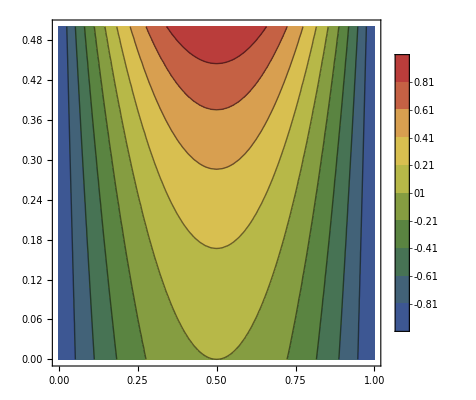

```mathematica
ContourPlot[(1-4 k+4 k^2-wG)/(-1+wG), {k,0,1},{wG,0,1/2}, PlotRange->{-1,1},ColorFunction->ColorData["DarkRainbow"], PlotLegends-> Automatic]
```

## Miscellany

### Stability conditions under full selfing (w/ generalized homozygote fitnesses)... to justify statement that stability occurs when 0 ≤ wAA, waa <1/2

```mathematica
Clear[x,y,z,xa,ya,za,F,p,q,w,wG,w2,wAA,waa,ks1,ke1,pa,qa, Fprime,S]
```

```mathematica
p = 1-q;
```

```mathematica
x =  (p^2)+F*p*q;
```

```mathematica
y = 2*p*q*(1-F);
```

```mathematica
z = q^2+F*p*q;
```

```mathematica
w = x*(wAA) +y +z*(waa);
```

```mathematica
xa = x*(wAA/w);
```

```mathematica
ya = y*(1/w);
```

```mathematica
za = z*(waa/w);
```

```mathematica
pa = ya*(1/2)+xa;
```

```mathematica
qa= ya*(1/2) +za;
```

```mathematica
xprime = S*(xa+ya*(1/4))+(1-S)*(pa^2);
```

```mathematica
yprime = S*ya*(1/2)+(1-S)*(2*pa*qa);
```

```mathematica
zprime = S*(za +ya*(1/4))+(1-S)*(qa^2);
```

```mathematica
pprime = xprime +yprime/2;
```

```mathematica
qprime = Simplify[zprime + yprime/2/. {S->1}];
```

```mathematica
Fprime = Simplify[1 - yprime/(2*pprime*qprime) /. {S->1}]
```

(-wAA-2 q (-1+waa) wAA+F^2 (-1+q) q (-wAA+waa (-1+2 wAA))+q^2 (-wAA+waa (-1+2 wAA))+F (wAA-3 q wAA-2 waa wAA+q waa (-1+4 wAA)+2 q^2 (waa+wAA-2 waa wAA)))/(2 (-1+q+F (-1+q) (-1+waa)-q waa) ((-1+F) q (-1+wAA)+wAA))

```mathematica
wa = Simplify[(qprime/pprime)/(q/p)/. {S->1}]
```

(1+q (-1+waa)+F (-1+q+waa-q waa))/((-1+F) q (-1+wAA)+wAA)

Upon obtaining expressions for the fitness of the “a” allele (wa) and the inbreeding coefficient (F), the equilibria can be obtained.

```mathematica
Simplify[Solve[wa ==1 &&  Fprime-F==0, {q,F}]]
```

{{q→((-1+waa) (-1+2 wAA))/(2-3 wAA+waa (-3+4 wAA)),F→(waa+wAA-2 waa wAA)/(2-2 waa-2 wAA+2 waa wAA)}}

Here I test for the biological feasibility of the equilibria. That is, I test whether the inbreeding coefficient generally lies in [-1,1].

```mathematica
Reduce[0≤ ((-1+waa) (-1+2 wAA))/(2-3 wAA+waa (-3+4 wAA))≤ 1 &&-1≤(waa+wAA-2 waa wAA)/(2-2 waa-2 wAA+2 waa wAA)≤1&&0≤wAA<1&&0≤waa≤ 1]
```

(0≤wAA<1/2&&0≤waa≤1/2)||(wAA==1/2&&0≤waa<1/2)

The preceding analysis identifies the biologically relevant equilibrium of q and F:

```mathematica
qhat = ((-1+waa) (-1+2 wAA))/(2-3 wAA+waa (-3+4 wAA));
```

```mathematica
Fhat =(waa+wAA-2 waa wAA)/(2-2 waa-2 wAA+2 waa wAA);
```

Here I set up the Jacobian, derive eigenvalues, and test for stability.

```mathematica
Simplify[{{D[qprime,q],D[qprime,F]},{D[Fprime,q], D[Fprime,F]}}/. {q-> qhat, F -> Fhat}]
```

{{(2 (-(-1+wAA) wAA+waa^2 (-1+2 wAA)+waa (1-4 wAA+2 wAA^2)))/(2-3 wAA+waa (-3+4 wAA)),(4 (-1+waa)^2 (-1+2 waa) (waa-wAA) (-1+wAA)^2 (-1+2 wAA))/(2-3 wAA+waa (-3+4 wAA))^3},{((waa-wAA) (2-3 wAA+waa (-3+4 wAA)))/((-1+waa) (-1+wAA)),(2 (2 waa^2 (-1+wAA)+wAA-2 wAA^2+waa (1-2 wAA+2 wAA^2)))/(2-3 wAA+waa (-3+4 wAA))}}

```mathematica
Eigenvalues[{{(2 (-(-1+wAA) wAA+waa^2 (-1+2 wAA)+waa (1-4 wAA+2 wAA^2)))/(2-3 wAA+waa (-3+4 wAA)),(4 (-1+waa)^2 (-1+2 waa) (waa-wAA) (-1+wAA)^2 (-1+2 wAA))/(2-3 wAA+waa (-3+4 wAA))^3},{((waa-wAA) (2-3 wAA+waa (-3+4 wAA)))/((-1+waa) (-1+wAA)),(2 (2 waa^2 (-1+wAA)+wAA-2 wAA^2+waa (1-2 wAA+2 wAA^2)))/(2-3 wAA+waa (-3+4 wAA))}}]
```

{(2 (-waa+waa^2))/(-1+waa),(2 (-wAA+wAA^2))/(-1+wAA)}

```mathematica
Reduce[Abs[(2 (-waa+waa^2))/(-1+waa)] <1 && Abs[(2 (-wAA+wAA^2))/(-1+wAA)]<1&& ((0≤wAA<1/2&&0≤waa≤1/2)||(wAA==1/2&&0≤waa<1/2))]
```

0≤wAA<1/2&&0≤waa<1/2

### Stability of A&N with generalized homozygous fitnesses to the direct invasion of Mendelian ratios

#### Single-locus model

```mathematica
Clear[x,y,z,xa,ya,za,F,p,q,w,wG,w2,u,v, Fprime, ke, ks,s]
```

```mathematica
p = 1-q;
```

```mathematica
x =  (p^2)+F*p*q;
```

```mathematica
y = 2*p*q*(1-F);
```

```mathematica
z = q^2+F*p*q;
```

```mathematica
w = x*(wAA) +y +z*(waa);
```

```mathematica
xa = x*(wAA/w);
```

```mathematica
ya = y*(1/w);
```

```mathematica
za = z*(waa/w);
```

```mathematica
u = ya*(1)+za;
```

```mathematica
v= ya*(0) +za;
```

```mathematica
xprime = S*(xa+ya*(1)*(0))+(1-S)*(1-u)*(1-v);
```

```mathematica
yprime = S*ya*((1)*(1)+(0)*(0))+(1-S)*((1-u)*v + u*(1-v));
```

```mathematica
zprime = S*(ya*((0)*(1)) +za)+(1-S)*u*v;
```

```mathematica
pprime = xprime +yprime/2;
```

```mathematica
qprime = Simplify[zprime + yprime/2];
```

```mathematica
Fprime = Simplify[1 - yprime/(2*pprime*qprime)]
```

(-F S waa wAA-(-1+F)^2 q (-1+S waa wAA)+(-1+F)^2 q^2 (-1+S waa wAA))/((-1+q+F (-1+q) (-1+waa)-q waa) ((-1+F) q (-1+wAA)+wAA))

```mathematica
wa = Simplify[(qprime/pprime)/(q/p)]
```

(1+q (-1+waa)+F (-1+q+waa-q waa))/((-1+F) q (-1+wAA)+wAA)

#### Equilibria

Upon obtaining expressions for the fitness of the “a” allele (wa) and the inbreeding coefficient (F), the equilibria can be obtained.

```mathematica
Simplify[Solve[wa ==1 &&  Fprime-F==0, {q,F}]]
```

{{q→1/2,F→-1},{q→1/(4 (-1+S) waa wAA (-2+waa+wAA))(waa^2 (-1+(-1+3 S) wAA)+wAA (wAA-√(wAA^2+2 waa wAA (-3+S (4-3 wAA)+wAA)+waa^2 (1+(2-6 S) wAA+(1+S)^2 wAA^2)))+waa (-4 (-1+S) wAA+(-3+S) wAA^2+√(wAA^2+2 waa wAA (-3+S (4-3 wAA)+wAA)+waa^2 (1+(2-6 S) wAA+(1+S)^2 wAA^2)))),F→(-2+waa+wAA+waa wAA-S waa wAA-√(-4 (-1+waa+wAA-waa wAA) (-1+S waa wAA)+(2-wAA+waa (-1+(-1+S) wAA))^2))/(2 (-1+waa+wAA-waa wAA))},{q→1/(4 (-1+S) waa wAA (-2+waa+wAA))(waa^2 (-1+(-1+3 S) wAA)+wAA (wAA+√(wAA^2+2 waa wAA (-3+S (4-3 wAA)+wAA)+waa^2 (1+(2-6 S) wAA+(1+S)^2 wAA^2)))-waa (4 (-1+S) wAA-(-3+S) wAA^2+√(wAA^2+2 waa wAA (-3+S (4-3 wAA)+wAA)+waa^2 (1+(2-6 S) wAA+(1+S)^2 wAA^2)))),F→(-2+waa+wAA+waa wAA-S waa wAA+√(-4 (-1+waa+wAA-waa wAA) (-1+S waa wAA)+(2-wAA+waa (-1+(-1+S) wAA))^2))/(2 (-1+waa+wAA-waa wAA))}}

```mathematica
Reduce[0< 1/(4 (-1+S) waa wAA (-2+waa+wAA))(waa^2 (-1+(-1+3 S) wAA)+wAA (wAA-√(wAA^2+2 waa wAA (-3+S (4-3 wAA)+wAA)+waa^2 (1+(2-6 S) wAA+(1+S)^2 wAA^2)))+waa (-4 (-1+S) wAA+(-3+S) wAA^2+√(wAA^2+2 waa wAA (-3+S (4-3 wAA)+wAA)+waa^2 (1+(2-6 S) wAA+(1+S)^2 wAA^2))))<1 && -1≤ (-2+waa+wAA+waa wAA-S waa wAA-√(-4 (-1+waa+wAA-waa wAA) (-1+S waa wAA)+(2-wAA+waa (-1+(-1+S) wAA))^2))/(2 (-1+waa+wAA-waa wAA))≤ 1 && 0≤ wAA <1 && 0≤ waa<1 && 0< S≤ 1]
```

False

```mathematica
Reduce[0< 1/(4 (-1+S) waa wAA (-2+waa+wAA))(waa^2 (-1+(-1+3 S) wAA)+wAA (wAA+√(wAA^2+2 waa wAA (-3+S (4-3 wAA)+wAA)+waa^2 (1+(2-6 S) wAA+(1+S)^2 wAA^2)))-waa (4 (-1+S) wAA-(-3+S) wAA^2+√(wAA^2+2 waa wAA (-3+S (4-3 wAA)+wAA)+waa^2 (1+(2-6 S) wAA+(1+S)^2 wAA^2))))<1 && -1≤(-2+waa+wAA+waa wAA-S waa wAA+√(-4 (-1+waa+wAA-waa wAA) (-1+S waa wAA)+(2-wAA+waa (-1+(-1+S) wAA))^2))/(2 (-1+waa+wAA-waa wAA))≤ 1 && 0≤ wAA <1 && 0≤ waa<1 && 0< S< 1, {S, wAA, waa}]
```

False

```mathematica
qhat = 1/2;
```

```mathematica
Fhat =  -1;
```

```mathematica
phat = 1 - qhat;
```

```mathematica
xhat = Simplify[(1-qhat)^2+(1-qhat)*(qhat)*Fhat ]
```

0

```mathematica
yhat = Simplify[2*(1-qhat)*(qhat)*(1-Fhat)]
```

1

```mathematica
zhat = Simplify[(qhat)^2+(1-qhat)*(qhat)*Fhat]
```

0

#### Direct invasion of Mendelian ratios in both sexes (into an A&N resident pop)

```mathematica
JacobianSelfing=
{{D[ABABprime, ABAB],D[ABABprime, aBaB], D[ABABprime, ABaB],D[ABABprime, ABAb],D[ABABprime, ABab], D[ABABprime, AbaB],D[ABABprime, aBab],D[ABABprime, AbAb],D[ABABprime, Abab],  D[ABABprime, abab]},{D[aBaBprime, ABAB],D[aBaBprime, aBaB], D[aBaBprime, ABaB],D[aBaBprime, ABAb],D[aBaBprime, ABab], D[aBaBprime, AbaB],D[aBaBprime, aBab],D[aBaBprime, AbAb],D[aBaBprime, Abab],  D[aBaBprime, abab]},
{D[ABaBprime, ABAB],D[ABaBprime, aBaB], D[ABaBprime, ABaB],D[ABaBprime, ABAb],D[ABaBprime, ABab], D[ABaBprime, AbaB],D[ABaBprime, aBab],D[ABaBprime, AbAb],D[ABaBprime, Abab],  D[ABaBprime, abab]},
{D[ABAbprime, ABAB],D[ABAbprime, aBaB], D[ABAbprime, ABaB],D[ABAbprime, ABAb],D[ABAbprime, ABab], D[ABAbprime, AbaB],D[ABAbprime, aBab],D[ABAbprime, AbAb],D[ABAbprime, Abab],  D[ABAbprime, abab]},
{D[ABabprime, ABAB],D[ABabprime, aBaB], D[ABabprime, ABaB],D[ABabprime, ABAb],D[ABabprime, ABab], D[ABabprime, AbaB],D[ABabprime, aBab],D[ABabprime, AbAb],D[ABabprime, Abab],  D[ABabprime, abab]},
{D[AbaBprime, ABAB],D[AbaBprime, aBaB], D[AbaBprime, ABaB],D[AbaBprime, ABAb],D[AbaBprime, ABab], D[AbaBprime, AbaB],D[AbaBprime, aBab],D[AbaBprime, AbAb],D[AbaBprime, Abab],  D[AbaBprime, abab]},
{D[aBabprime, ABAB],D[aBabprime, aBaB], D[aBabprime, ABaB],D[aBabprime, ABAb],D[aBabprime, ABab], D[aBabprime, AbaB],D[aBabprime, aBab],D[aBabprime, AbAb],D[aBabprime, Abab],  D[aBabprime, abab]},
{D[AbAbprime, ABAB],D[AbAbprime, aBaB], D[AbAbprime, ABaB],D[AbAbprime, ABAb],D[AbAbprime, ABab], D[AbAbprime, AbaB],D[AbAbprime, aBab],D[AbAbprime, AbAb],D[AbAbprime, Abab],  D[AbAbprime, abab]},
{D[Ababprime, ABAB],D[Ababprime, aBaB], D[Ababprime, ABaB],D[Ababprime, ABAb],D[Ababprime, ABab], D[Ababprime, AbaB],D[Ababprime, aBab],D[Ababprime, AbAb],D[Ababprime, Abab],  D[Ababprime, abab]},
{D[ababprime, ABAB],D[ababprime, aBaB], D[ababprime, ABaB],D[ababprime, ABAb],D[ababprime, ABab], D[ababprime, AbaB],D[ababprime, aBab],D[ababprime, AbAb],D[ababprime, Abab],  D[ababprime, abab]}}/.{ r->1/2,ke1->0,ks1->1,ke2 -> 1/2, ks2 -> 1/2,wAa->1, ABAB->0,aBaB->0,ABaB->1,ABAb->0,ABab->0,AbaB->0,aBab->0,AbAb->0,Abab->0,abab->0};
```

```mathematica
Jmut = JacobianSelfing[[4;;10, 4;;10]]
```

{{1/2 (1-S) wAA+(S wAA)/2,(1-S)/4+S/8,(1-S)/4+S/8,0,(1-S) wAA,(1-S)/2,0},{0,(1-S)/4+S/8,(1-S)/4+S/8,1/2 (1-S) waa,0,(1-S)/2,(1-S) waa},{1/2 (1-S) wAA,(1-S)/4+S/8,(1-S)/4+S/8,0,(1-S) wAA,(1-S)/2,0},{0,(1-S)/4+S/8,(1-S)/4+S/8,1/2 (1-S) waa+(S waa)/2,0,(1-S)/2,(1-S) waa},{(S wAA)/4,S/16,S/16,0,S wAA,S/4,0},{0,S/8,S/8,0,0,S/2,0},{0,S/16,S/16,(S waa)/4,0,S/4,S waa}}

```mathematica
Simplify[Eigenvalues[Jmut]]
```

{0,S/4,(S waa)/2,(S wAA)/2,1/16 Root[-1024 S waa wAA-1024 S^2 waa wAA+(32 waa+96 S waa+32 wAA+96 S wAA+64 waa wAA+128 S waa wAA+64 S^2 waa wAA) #1+(-8-8 waa-8 S waa-8 wAA-8 S wAA) #1^2+#1^3&,1],1/16 Root[-1024 S waa wAA-1024 S^2 waa wAA+(32 waa+96 S waa+32 wAA+96 S wAA+64 waa wAA+128 S waa wAA+64 S^2 waa wAA) #1+(-8-8 waa-8 S waa-8 wAA-8 S wAA) #1^2+#1^3&,2],1/16 Root[-1024 S waa wAA-1024 S^2 waa wAA+(32 waa+96 S waa+32 wAA+96 S wAA+64 waa wAA+128 S waa wAA+64 S^2 waa wAA) #1+(-8-8 waa-8 S waa-8 wAA-8 S wAA) #1^2+#1^3&,3]}

```mathematica
Reduce[-1<1/16 Root[-1024 S waa wAA-1024 S^2 waa wAA+(32 waa+96 S waa+32 wAA+96 S wAA+64 waa wAA+128 S waa wAA+64 S^2 waa wAA) #1+(-8-8 waa-8 S waa-8 wAA-8 S wAA) #1^2+#1^3&,1]<1 && 0≤ wAA <1 && 0 ≤ waa < 1 && 0<S<1]
```

0<S<1&&0≤wAA<1&&0≤waa<1

```mathematica
Reduce[-1<1/16 Root[-1024 S waa wAA-1024 S^2 waa wAA+(32 waa+96 S waa+32 wAA+96 S wAA+64 waa wAA+128 S waa wAA+64 S^2 waa wAA) #1+(-8-8 waa-8 S waa-8 wAA-8 S wAA) #1^2+#1^3&,2]<1 && 0≤ wAA <1 && 0 ≤ waa < 1 && 0<S<1]
```

0<S<1&&0≤wAA<1&&0≤waa<1

```mathematica
Reduce[1/16 Root[-1024 S waa wAA-1024 S^2 waa wAA+(32 waa+96 S waa+32 wAA+96 S wAA+64 waa wAA+128 S waa wAA+64 S^2 waa wAA) #1+(-8-8 waa-8 S waa-8 wAA-8 S wAA) #1^2+#1^3&,3]<1 && 0≤ wAA <1 && 0 ≤ waa < 1 && 0<S<1]
```

0≤wAA<1&&0≤waa<1&&0<S<1

#### Direct invasion of Male-limited Mendelian segregation (w/ no change in females), into a resident A&N pop

```mathematica
JacobianSelfing=
{{D[ABABprime, ABAB],D[ABABprime, aBaB], D[ABABprime, ABaB],D[ABABprime, ABAb],D[ABABprime, ABab], D[ABABprime, AbaB],D[ABABprime, aBab],D[ABABprime, AbAb],D[ABABprime, Abab],  D[ABABprime, abab]},{D[aBaBprime, ABAB],D[aBaBprime, aBaB], D[aBaBprime, ABaB],D[aBaBprime, ABAb],D[aBaBprime, ABab], D[aBaBprime, AbaB],D[aBaBprime, aBab],D[aBaBprime, AbAb],D[aBaBprime, Abab],  D[aBaBprime, abab]},
{D[ABaBprime, ABAB],D[ABaBprime, aBaB], D[ABaBprime, ABaB],D[ABaBprime, ABAb],D[ABaBprime, ABab], D[ABaBprime, AbaB],D[ABaBprime, aBab],D[ABaBprime, AbAb],D[ABaBprime, Abab],  D[ABaBprime, abab]},
{D[ABAbprime, ABAB],D[ABAbprime, aBaB], D[ABAbprime, ABaB],D[ABAbprime, ABAb],D[ABAbprime, ABab], D[ABAbprime, AbaB],D[ABAbprime, aBab],D[ABAbprime, AbAb],D[ABAbprime, Abab],  D[ABAbprime, abab]},
{D[ABabprime, ABAB],D[ABabprime, aBaB], D[ABabprime, ABaB],D[ABabprime, ABAb],D[ABabprime, ABab], D[ABabprime, AbaB],D[ABabprime, aBab],D[ABabprime, AbAb],D[ABabprime, Abab],  D[ABabprime, abab]},
{D[AbaBprime, ABAB],D[AbaBprime, aBaB], D[AbaBprime, ABaB],D[AbaBprime, ABAb],D[AbaBprime, ABab], D[AbaBprime, AbaB],D[AbaBprime, aBab],D[AbaBprime, AbAb],D[AbaBprime, Abab],  D[AbaBprime, abab]},
{D[aBabprime, ABAB],D[aBabprime, aBaB], D[aBabprime, ABaB],D[aBabprime, ABAb],D[aBabprime, ABab], D[aBabprime, AbaB],D[aBabprime, aBab],D[aBabprime, AbAb],D[aBabprime, Abab],  D[aBabprime, abab]},
{D[AbAbprime, ABAB],D[AbAbprime, aBaB], D[AbAbprime, ABaB],D[AbAbprime, ABAb],D[AbAbprime, ABab], D[AbAbprime, AbaB],D[AbAbprime, aBab],D[AbAbprime, AbAb],D[AbAbprime, Abab],  D[AbAbprime, abab]},
{D[Ababprime, ABAB],D[Ababprime, aBaB], D[Ababprime, ABaB],D[Ababprime, ABAb],D[Ababprime, ABab], D[Ababprime, AbaB],D[Ababprime, aBab],D[Ababprime, AbAb],D[Ababprime, Abab],  D[Ababprime, abab]},
{D[ababprime, ABAB],D[ababprime, aBaB], D[ababprime, ABaB],D[ababprime, ABAb],D[ababprime, ABab], D[ababprime, AbaB],D[ababprime, aBab],D[ababprime, AbAb],D[ababprime, Abab],  D[ababprime, abab]}}/.{ r->1/2,ke1->0,ks1->1,ke2 -> 0, ks2 -> 1/2,wAa->1, ABAB->0,aBaB->0,ABaB->1,ABAb->0,ABab->0,AbaB->0,aBab->0,AbAb->0,Abab->0,abab->0};
```

```mathematica
Jmut = JacobianSelfing[[4;;10, 4;;10]]
```

{{1/2 (1-S) wAA+(S wAA)/2,(1-S)/4+S/4,(1-S)/4+S/4,0,(1-S) wAA,(1-S)/2,0},{0,(1-S)/4+S/8,(1-S)/4+S/8,1/2 (1-S) waa,0,(1-S)/2,(1-S) waa},{1/2 (1-S) wAA,(1-S)/2+S/8,(1-S)/2+S/8,0,(1-S) wAA,1-S,0},{0,0,0,1/2 (1-S) waa+(S waa)/2,0,0,(1-S) waa},{(S wAA)/4,S/8,S/8,0,S wAA,S/2,0},{0,S/8,S/8,0,0,S/2,0},{0,0,0,(S waa)/4,0,0,S waa}}

```mathematica
Simplify[Eigenvalues[Jmut]]
```

{0,S/4,(S waa)/2,1/2 (1+S) waa,(S wAA)/2,1/8 (3-S+2 wAA+2 S wAA-1/2 √(-64 (1+S) wAA+4 (3+2 wAA+S (-1+2 wAA))^2)),1/8 (3-S+2 wAA+2 S wAA+1/2 √(-64 (1+S) wAA+4 (3+2 wAA+S (-1+2 wAA))^2))}

```mathematica
Reduce[-1<1/8 (3-S+2 wAA+2 S wAA-1/2 √(-64 (1+S) wAA+4 (3+2 wAA+S (-1+2 wAA))^2))<1 && 0≤ wAA <1 && 0 ≤ waa < 1 && 0<S<1]
```

0≤waa<1&&0≤wAA<1&&0<S<1

```mathematica
Reduce[-1<1/8 (3-S+2 wAA+2 S wAA+1/2 √(-64 (1+S) wAA+4 (3+2 wAA+S (-1+2 wAA))^2))<1 && 0≤ wAA <1 && 0 ≤ waa < 1 && 0<S<1]
```

0≤waa<1&&0≤wAA<1&&0<S<1

#### Direct invasion of Female-limited Mendelian segregation (w/ no change in males), into a resident A&N pop

```mathematica
JacobianSelfing=
{{D[ABABprime, ABAB],D[ABABprime, aBaB], D[ABABprime, ABaB],D[ABABprime, ABAb],D[ABABprime, ABab], D[ABABprime, AbaB],D[ABABprime, aBab],D[ABABprime, AbAb],D[ABABprime, Abab],  D[ABABprime, abab]},{D[aBaBprime, ABAB],D[aBaBprime, aBaB], D[aBaBprime, ABaB],D[aBaBprime, ABAb],D[aBaBprime, ABab], D[aBaBprime, AbaB],D[aBaBprime, aBab],D[aBaBprime, AbAb],D[aBaBprime, Abab],  D[aBaBprime, abab]},
{D[ABaBprime, ABAB],D[ABaBprime, aBaB], D[ABaBprime, ABaB],D[ABaBprime, ABAb],D[ABaBprime, ABab], D[ABaBprime, AbaB],D[ABaBprime, aBab],D[ABaBprime, AbAb],D[ABaBprime, Abab],  D[ABaBprime, abab]},
{D[ABAbprime, ABAB],D[ABAbprime, aBaB], D[ABAbprime, ABaB],D[ABAbprime, ABAb],D[ABAbprime, ABab], D[ABAbprime, AbaB],D[ABAbprime, aBab],D[ABAbprime, AbAb],D[ABAbprime, Abab],  D[ABAbprime, abab]},
{D[ABabprime, ABAB],D[ABabprime, aBaB], D[ABabprime, ABaB],D[ABabprime, ABAb],D[ABabprime, ABab], D[ABabprime, AbaB],D[ABabprime, aBab],D[ABabprime, AbAb],D[ABabprime, Abab],  D[ABabprime, abab]},
{D[AbaBprime, ABAB],D[AbaBprime, aBaB], D[AbaBprime, ABaB],D[AbaBprime, ABAb],D[AbaBprime, ABab], D[AbaBprime, AbaB],D[AbaBprime, aBab],D[AbaBprime, AbAb],D[AbaBprime, Abab],  D[AbaBprime, abab]},
{D[aBabprime, ABAB],D[aBabprime, aBaB], D[aBabprime, ABaB],D[aBabprime, ABAb],D[aBabprime, ABab], D[aBabprime, AbaB],D[aBabprime, aBab],D[aBabprime, AbAb],D[aBabprime, Abab],  D[aBabprime, abab]},
{D[AbAbprime, ABAB],D[AbAbprime, aBaB], D[AbAbprime, ABaB],D[AbAbprime, ABAb],D[AbAbprime, ABab], D[AbAbprime, AbaB],D[AbAbprime, aBab],D[AbAbprime, AbAb],D[AbAbprime, Abab],  D[AbAbprime, abab]},
{D[Ababprime, ABAB],D[Ababprime, aBaB], D[Ababprime, ABaB],D[Ababprime, ABAb],D[Ababprime, ABab], D[Ababprime, AbaB],D[Ababprime, aBab],D[Ababprime, AbAb],D[Ababprime, Abab],  D[Ababprime, abab]},
{D[ababprime, ABAB],D[ababprime, aBaB], D[ababprime, ABaB],D[ababprime, ABAb],D[ababprime, ABab], D[ababprime, AbaB],D[ababprime, aBab],D[ababprime, AbAb],D[ababprime, Abab],  D[ababprime, abab]}}/.{ r->1/2,ke1->0,ks1->1,ke2 -> 1/2, ks2 -> 1,wAa->1, ABAB->0,aBaB->0,ABaB->1,ABAb->0,ABab->0,AbaB->0,aBab->0,AbAb->0,Abab->0,abab->0};
```

```mathematica
Jmut = JacobianSelfing[[4;;10, 4;;10]]
```

{{1/2 (1-S) wAA+(S wAA)/2,0,0,0,(1-S) wAA,0,0},{0,(1-S)/2+S/8,(1-S)/2+S/8,1/2 (1-S) waa,0,1-S,(1-S) waa},{1/2 (1-S) wAA,(1-S)/4+S/8,(1-S)/4+S/8,0,(1-S) wAA,(1-S)/2,0},{0,(1-S)/4+S/4,(1-S)/4+S/4,1/2 (1-S) waa+(S waa)/2,0,(1-S)/2,(1-S) waa},{(S wAA)/4,0,0,0,S wAA,0,0},{0,S/8,S/8,0,0,S/2,0},{0,S/8,S/8,(S waa)/4,0,S/2,S waa}}

```mathematica
Simplify[Eigenvalues[Jmut]]
```

{0,S/4,(S waa)/2,1/8 (3-S+2 waa+2 S waa-1/2 √(-64 (1+S) waa+4 (3+2 waa+S (-1+2 waa))^2)),1/8 (3-S+2 waa+2 S waa+1/2 √(-64 (1+S) waa+4 (3+2 waa+S (-1+2 waa))^2)),(S wAA)/2,1/2 (1+S) wAA}

```mathematica
Reduce[-1<1/8 (3-S+2 waa+2 S waa-1/2 √(-64 (1+S) waa+4 (3+2 waa+S (-1+2 waa))^2))<1 && 0≤ wAA <1 && 0 ≤ waa < 1 && 0<S<1]
```

0≤wAA<1&&0≤waa<1&&0<S<1

```mathematica
Reduce[-1<1/8 (3-S+2 waa+2 S waa+1/2 √(-64 (1+S) waa+4 (3+2 waa+S (-1+2 waa))^2))<1 && 0≤ wAA <1 && 0 ≤ waa < 1 && 0<S<1]
```

0≤wAA<1&&0≤waa<1&&0<S<1